```mathematica
Dt[x]
```

Dt[x]

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[f[g[x]]]
```

Dt[x] f'[g[x]] g'[x]

```mathematica
Composition[f,g,h][x]
```

f[g[h[x]]]

```mathematica
Composition[f,g,h]
```

f@*g@*h

```mathematica
RightComposition[f,g,h]
```

f/*g/*h

```mathematica
(f@*g@*h)[x]
```

f[g[h[x]]]

```mathematica
InverseFunction[Composition[f,g,h]]
```

h^(-1)@*g^(-1)@*f^(-1)

```mathematica
D[α x^2]
```

x^2 α

```mathematica
Dt[α x^2]
```

2 x α Dt[x]+x^2 Dt[α]

```mathematica
Dt[f[x]g[x]]
```

Dt[x] g[x] f'[x]+Dt[x] f[x] g'[x]

```mathematica
Dt[x] (g[x] f'[x]+f[x] g'[x])
```

Dt[x] (g[x] f'[x]+f[x] g'[x])

```mathematica
x Sin[x x]
```

x Sin[x^2]

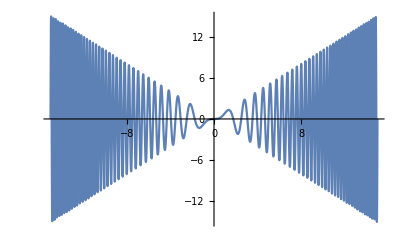

```mathematica
Plot[x Sin[x^2],{x,-15.039769647786,15.039769647786}]
```

```mathematica
Dt[x Sin[x^2]]
```

2 x^2 Cos[x^2] Dt[x]+Dt[x] Sin[x^2]

```mathematica
∫x𝕕x
```

Integrate::nodiffd: ∫x𝕕x cannot be interpreted. Integrals are entered in the form ∫fⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc.

```mathematica
ⅆ
```

```mathematica
InputForm@ⅆ
```

```mathematica
∫ⅆx
```

x

```mathematica
Dt[Composition[f,g,h][x]]
```

Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]

```mathematica
∫√(1-x^2)ⅆx
```

1/2 (x √(1-x^2)+ArcSin[x])

```mathematica
ExpandAll[1/2 (x √(1-x^2)+ArcSin[x])]
```

1/2 x √(1-x^2)+ArcSin[x]/2

```mathematica
Dt[1/2 x √(1-x^2)+ArcSin[x]/2]==√(1-x^2)
```

Dt[x]/(2 √(1-x^2))-(x^2 Dt[x])/(2 √(1-x^2))+1/2 √(1-x^2) Dt[x]==√(1-x^2)

```mathematica
(1/(2 √(1-x^2))-x^2/(2 √(1-x^2))+1/2 √(1-x^2) )Dt[x]==√(1-x^2)
```

(1/(2 √(1-x^2))-x^2/(2 √(1-x^2))+(√(1-x^2))/2) Dt[x]==√(1-x^2)

```mathematica
Dt[a x^n,x]
```

x^n Dt[a,x]+a x^n (n/x+Dt[n,x] Log[x])

```mathematica
Dt[a x^n]
```

x^n Dt[a]+a x^n ((n Dt[x])/x+Dt[n] Log[x])

```mathematica
Dt[f g]
```

g Dt[f]+f Dt[g]

```mathematica
1/2(1/(√(1-x^2))-x^2/(√(1-x^2))+√(1-x^2)) Dt[x]==√(1-x^2)
```

1/2 (1/(√(1-x^2))-x^2/(√(1-x^2))+√(1-x^2)) Dt[x]==√(1-x^2)

```mathematica
Dt[a b c]
```

b c Dt[a]+a c Dt[b]+a b Dt[c]

```mathematica
ComplexPlot[((z^2-1)(z+2-I)^2)/(z^2+2-2I),{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
(G Subscript[m, 1] Subscript[m, 2])/r^2
```

(G m_1 m_2)/r^2

```mathematica
2(G Subscript[m, 1] Subscript[m, 2])/r^2==(G Subscript[m, 1] Subscript[m, 2])/(r+k)^2
```

(2 G m_1 m_2)/r^2==(G m_1 m_2)/(k+r)^2

```mathematica
Solve[2(G Subscript[m, 1] Subscript[m, 2])/r^2==(G Subscript[m, 1] Subscript[m, 2])/(r+k)^2{k}]
```

{{G→0},{k→1/4 (-4 r-√(-8+r) r^(3/2)+r^2)},{k→1/4 (-4 r+√(-8+r) r^(3/2)+r^2)},{m_1→0},{m_2→0}}

```mathematica
Solve[2(G Subscript[m, 1] Subscript[m, 2])/r^2==(G Subscript[m, 1] Subscript[m, 2])/(r+k)^2,{k},Reals]
```

{{k→-r-(√(r^2))/(√2)},{k→-r+(√(r^2))/(√2)}}

```mathematica
Solve[2(G Subscript[m, 1] Subscript[m, 2])/r^2==(G (Subscript[m, 1]+k)Subscript[m, 2])/r^2,{k},Reals]
```

{{k→ConditionalExpression[m_1,r>0||r<0]}}

```mathematica
Dt[(G Subscript[m, 1] Subscript[m, 2])/r^2]
```

(Dt[G] m_1 m_2)/r^2-(2 G Dt[r] m_1 m_2)/r^3+(G Dt[m] m_2 Subscript^(1,0)[m,1])/r^2+(G Dt[m] m_1 Subscript^(1,0)[m,2])/r^2

```mathematica
TraditionalForm[(Dt[G] Subscript[m, 1] Subscript[m, 2])/r^2-(2 G Dt[r] Subscript[m, 1] Subscript[m, 2])/r^3+(G Dt[m] Subscript[m, 2] Derivative[1,0][Subscript][m,1])/r^2+(G Dt[m] Subscript[m, 1] Derivative[1,0][Subscript][m,2])/r^2]
```

(G m_2 ⅆm Subscript^(1,0)(m,1))/r^2+(G m_1 ⅆm Subscript^(1,0)(m,2))/r^2-(2 G m_1 m_2 ⅆr)/r^3+(m_1 m_2 ⅆG)/r^2

```mathematica
Dt[f[x]^n,{x,n}]
```

Dt[f[x]^n,{x,n}]

```mathematica
Dt[f[x]^n,x]
```

f[x]^n (Dt[n,x] Log[f[x]]+(n f'[x])/f[x])

```mathematica
Dt[f[x]^n]
```

f[x]^n (Dt[n] Log[f[x]]+(n Dt[x] f'[x])/f[x])

```mathematica
ComplexPlot[z^2,{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[z^3,{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[2^z,{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[z,{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[Cos[z]+I Sin[z],{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
Normalize@{1,f'[x]}.Normalize@{0-x,1-f[x]}
```

-x/(√(Abs[x]^2+Abs[1-f[x]]^2) √(1+Abs[f'[x]]^2))+((1-f[x]) f'[x])/(√(Abs[x]^2+Abs[1-f[x]]^2) √(1+Abs[f'[x]]^2))

```mathematica
FullSimplify[
Normalize@{1,f'[x]}.Normalize@{0-x,1-f[x]}
,{x,f[x],f'[x]}∈Reals]
```

(-x-(-1+f[x]) f'[x])/(√((x^2+(-1+f[x])^2) (1+f'[x]^2)))

```mathematica
With[{f=Function[x,x x]},(-x-(-1+f[x]) f'[x])/(√((x^2+(-1+f[x])^2) (1+f'[x]^2)))]
```

(-x-2 x (-1+x^2))/(√((1+4 x^2) (x^2+(-1+x^2)^2)))

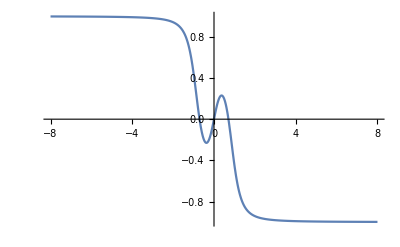

```mathematica
Plot[(-x-2 x (-1+x^2))/(√((1+4 x^2) (x^2+(-1+x^2)^2))),{x,-8,8}]
```

```mathematica
√(1+f'[x]^2)
```

√(1+f'[x]^2)

```mathematica
∫_a^b √(1+f'[x]^2)ⅆx
```

∫_a^b √(1+f'[x]^2)ⅆx

```mathematica
(x+y ⅈ)^2
```

(x+ⅈ y)^2

```mathematica
Expand[(x+ⅈ y)^2]
```

x^2+2 ⅈ x y-y^2

```mathematica
CoefficientList[x^2+2 ⅈ x y-y^2,{x,y}]
```

{{0,0,-1},{0,2 ⅈ,0},{1,0,0}}

```mathematica
Dt[u[x,y]+v[x,y]ⅈ]
```

Dt[y] u^(0,1)[x,y]+Dt[x] u^(1,0)[x,y]+ⅈ (Dt[y] v^(0,1)[x,y]+Dt[x] v^(1,0)[x,y])

```mathematica
√x==Sum[Subscript[a, i] x^i,{x,0,n}]
```

√x==(0^i+HarmonicNumber[n,-i]) a_i

```mathematica
√x==Sum[Subscript[a, i] x^i,{x,1,n}]
```

√x==HarmonicNumber[n,-i] a_i

```mathematica
{a,b}.{b,a}
```

2 a b

```mathematica
Conjugate[{a,b}]
```

{Conjugate[a],Conjugate[b]}

```mathematica
{b,a}.Conjugate[{a,b}]
```

b Conjugate[a]+a Conjugate[b]

```mathematica
Exp[f''[x]/f'[x]]
```

ⅇ^(f''[x]/f'[x])

```mathematica
With[{f=Identity},Exp[f''[x]/f'[x]]]
```

1

```mathematica
With[{f=Function[x,x x]},Exp[f''[x]/f'[x]]]
```

ⅇ^(1/x)

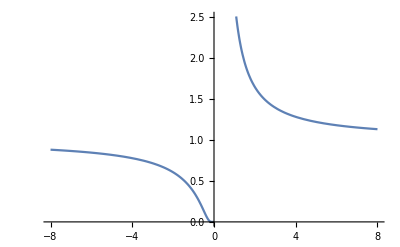

```mathematica
Plot[ⅇ^(1/x),{x,-8,8}]
```

```mathematica
With[{f=Function[x,x x]},Exp[f'[x]/f[x]]]
```

ⅇ^(2/x)

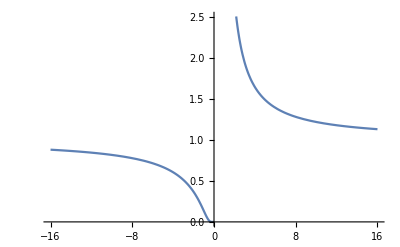

```mathematica
Plot[ⅇ^(2/x),{x,-16,16}]
```

```mathematica
With[{f=Function[x,x x x]},Exp[f''[x]/f'[x]]]
```

ⅇ^(2/x)

```mathematica
With[{f=Function[x,x x]},Exp[f'[x]/f[x]]]
```

ⅇ^(2/x)

```mathematica
Plot[ⅇ^(2/x),{x,-16,16}]
```

-Graphics-

```mathematica
MultinormalDistribution[1]
```

MultinormalDistribution::argr: MultinormalDistribution called with 1 argument; 2 arguments are expected.

MultinormalDistribution[1]

```mathematica
PDF[MultinormalDistribution[1,0],x]
```

MultinormalDistribution::vrprm: The value 1 at position 1 in MultinormalDistribution[1,0] is expected to be a list of real numbers.

PDF[MultinormalDistribution[1,0],x]

```mathematica
PDF[MultinormalDistribution[1,0],{x,y}]
```

MultinormalDistribution::vrprm: The value 1 at position 1 in MultinormalDistribution[1,0] is expected to be a list of real numbers.

PDF[MultinormalDistribution[1,0],{x,y}]

```mathematica
PDF[MultinormalDistribution[0,1],{x,y}]
```

MultinormalDistribution::vrprm: The value 0 at position 1 in MultinormalDistribution[0,1] is expected to be a list of real numbers.

PDF[MultinormalDistribution[0,1],{x,y}]

```mathematica
MultinormalDistribution[1,0]
```

MultinormalDistribution[1,0]

```mathematica
MultinormalDistribution[0,1]
```

MultinormalDistribution[0,1]

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
(ⅇ^(-(x y)^2/2))/(√(2 π))
```

(ⅇ^(-1/2 x^2 y^2))/(√(2 π))

```mathematica
Plot3D[(ⅇ^(-1/2 x^2 y^2))/(√(2 π)),{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Dt[(ⅇ^(-1/2 x^2 y^2))/(√(2 π))]
```

(ⅇ^(-1/2 x^2 y^2) (-x y^2 Dt[x]-x^2 y Dt[y]))/(√(2 π))

```mathematica
Dt[Composition[f,g,h][x]]
```

Dt[x] f'[g[h[x]]] g'[h[x]] h'[x]

```mathematica
Composition[f,g,h]
```

f@*g@*h

```mathematica
FullSimplify[
Normalize[{g'[x],h'[x]}].
Normalize[{1,f'[x]}]
,{x,f'[x],g'[x],h'[x]}]
```

((1+True) Sign[True])/(√(2+2 True Conjugate[True]))

```mathematica
FullSimplify[
Normalize[{g'[x],h'[x]}].
Normalize[{1,f'[x]}]==1
,{x,f'[x],g'[x],h'[x]}]
```

2 √(1+Abs[True]^2)==√2 (1+True) Sign[True]

```mathematica
Normalize[{g'[x],h'[x]}] . Normalize[{1,f'[x]}]==1
```

g'[x]/(√(1+Abs[f'[x]]^2) √(Abs[g'[x]]^2+Abs[h'[x]]^2))+(f'[x] h'[x])/(√(1+Abs[f'[x]]^2) √(Abs[g'[x]]^2+Abs[h'[x]]^2))==1

```mathematica
FullSimplify[
Normalize[{g'[x],h'[x]}].
Normalize[{1,f'[x]}]==1
,{x,f'[x],g'[x],h'[x]}∈Reals]
```

(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==1

```mathematica
DSolve[(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==1,{f[x],g[x],h[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==1,{f[x],g[x],h[x]},{x}]

```mathematica
DSolve[(g'[x]+f'[x] h'[x])/(√((1+f'[x]^2) (g'[x]^2+h'[x]^2)))==1,{f[x]},{x}]
```

{{f[x]→C[1]+h'[K[1]]/g'[K[1]]K[1]1x}}

```mathematica
{{f[x]->C[1]+h'[K[1]]/g'[K[1]]K[1]1x}}⟦1,1,2⟧
```

C[1]+h'[K[1]]/g'[K[1]]K[1]1x

```mathematica
Activate[h'[K[1]]/g'[K[1]]K[1]1x]
```

∫_1^x h'[K[1]]/g'[K[1]]ⅆK[1]

```mathematica
∫_1^s h'[K[1]]/g'[K[1]] ⅆK[1]/.K[1]->x
```

∫_1^s h'[x]/g'[x]ⅆx

```mathematica
E
```

ⅇ

```mathematica
u[x]==k[x]+p[x]
```

u[x]==k[x]+p[x]

```mathematica
k[x]==1/2 m v^2
```

k[x]==(m v^2)/2

```mathematica
p[x]==m g h
```

p[x]==g h m

```mathematica
k[x]-p[x]/.{k[x]->1/2 m v^2,p[x]->m g h }
```

-g h m+(m v^2)/2

```mathematica
D[-y[x] h m+(m y'[x]^2)/2,y[x]]
```

-h m

```mathematica
D[-y[x] h m+(m y'[x]^2)/2,y[x]]==D[D[-y[x] h m+(m y'[x]^2)/2,y'[x]],x]
```

-h m==m y''[x]

```mathematica
DSolve[-h m==m y''[x],{y[x]},{x}]
```

{{y[x]→-(h x^2)/2+C[1]+x C[2]}}

```mathematica
{x'[t]==1,y'[t]==-2}
```

{x'[t]==1,y'[t]==-2}

```mathematica
DSolve[{x'[t]==1,y'[t]==-2,x[0]==0,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→t,y[t]→-2 t}}

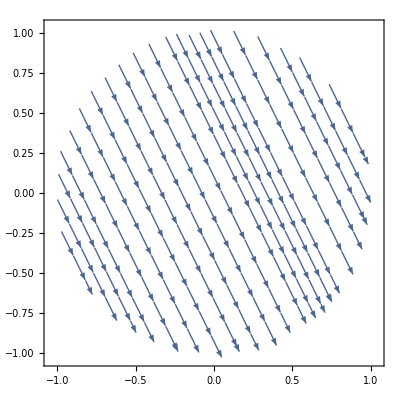

```mathematica
StreamPlot[
{1,-2}
,{x,y}∈Disk[]]
```

```mathematica
DSolve[{x'[t]==1,y'[t]==-2t,x[0]==0,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→t,y[t]→-t^2}}

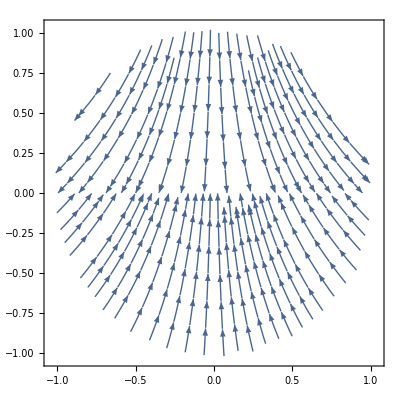

```mathematica
StreamPlot[
{x y,-y}
,{x,y}∈Disk[]]
```

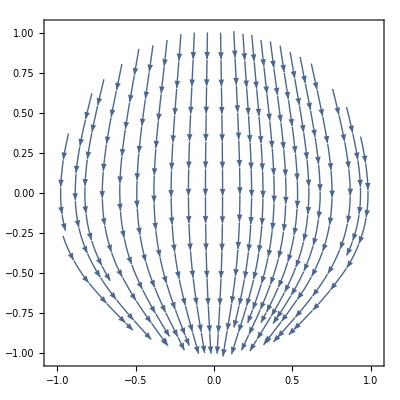

```mathematica
StreamPlot[
{x y,-Exp[y]}
,{x,y}∈Disk[]]
```

```mathematica
Integrate[1/(√(x^2-Sin[x])),x]
```

∫1/(√(x^2-Sin[x]))ⅆx

```mathematica
NIntegrate[1/(√(x^2-Sin[x])),x]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in x.

NIntegrate[1/(√(x^2-Sin[x])),x]

```mathematica
NIntegrate[1/(√(x^2-Sin[x])),{x,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.876938}. NIntegrate obtained 0.632707-2.8724 ⅈ and 0.0726222 for the integral and error estimates.

0.632707-2.8724 ⅈ

```mathematica
NIntegrate[1/(√(x^2-Sin[x])),{x,0,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.878751}. NIntegrate obtained 3.27697-2.86076 ⅈ and 0.169095 for the integral and error estimates.

3.27697-2.86076 ⅈ

```mathematica
Table[NIntegrate[1/(√(x^2-Sin[x])),{x,0,a}],{a,.1,50,.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.8767284216591401842244568598516707425005733966827392578125}. NIntegrate obtained 0.289955-2.85681 ⅈ and 0.00954017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.876938}. NIntegrate obtained 0.632707-2.8724 ⅈ and 0.0726222 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.878694}. NIntegrate obtained 0.849599-2.85494 ⅈ and 0.0213707 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
Table[NIntegrate[1/(√(x^2-Sin[x])),{x,0,a}],{a,1,50,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.876938}. NIntegrate obtained 0.632707-2.8724 ⅈ and 0.0726222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.878875}. NIntegrate obtained 1.69192-2.84306 ⅈ and 0.039828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.87886}. NIntegrate obtained 2.1801-2.79755 ⅈ and 0.119854 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.632707-2.8724 ⅈ,1.69192-2.84306 ⅈ,2.1801-2.79755 ⅈ,2.47128-2.77835 ⅈ,2.58994-2.89067 ⅈ,2.78453-2.85137 ⅈ,2.91865-2.94652 ⅈ,3.1416-2.77288 ⅈ,3.52009-2.75652 ⅈ,3.27697-2.86076 ⅈ,3.3769-2.85692 ⅈ,3.45744-2.85319 ⅈ,3.52249-2.83162 ⅈ,3.61796-2.86725 ⅈ,3.77668-2.82203 ⅈ,3.75931-2.84245 ⅈ,3.7832-2.81652 ⅈ,3.91059-2.82536 ⅈ,3.89893-2.84455 ⅈ,3.92773-2.8425 ⅈ,3.98877-2.87477 ⅈ,4.05059-2.90623 ⅈ,4.10064-2.95727 ⅈ,4.16435-2.84879 ⅈ,4.16995-2.82965 ⅈ,4.15857-2.92527 ⅈ,4.16529-2.92099 ⅈ,4.31155-2.85244 ⅈ,4.25429-2.85806 ⅈ,4.39819-2.76381 ⅈ,4.40001-2.83409 ⅈ,6.12202-2.6524 ⅈ,4.38741-2.98181 ⅈ,4.49772-2.89463 ⅈ,4.63139-2.79949 ⅈ,4.55512-2.88696 ⅈ,4.49158-3.00843 ⅈ,4.64611-2.78875 ⅈ,4.56992-3.24148 ⅈ,4.61467-2.91706 ⅈ,4.6821-2.72423 ⅈ,4.6345-2.88336 ⅈ,4.61565-2.84318 ⅈ,4.81247-2.61623 ⅈ,4.85896-2.80294 ⅈ,4.53099-3.16412 ⅈ,5.07249-2.68881 ⅈ,5.13566-2.6886 ⅈ,5.0818-2.70478 ⅈ,5.48283-2.70158 ⅈ}

```mathematica
DiscretePlot[Table[NIntegrate[1/(√(x^2-Sin[x])),{x,0,a}],{a,1,50,1}]]
```

DiscretePlot::argr: DiscretePlot called with 1 argument; 2 arguments are expected.

DiscretePlot[Table[NIntegrate[1/(√(x^2-Sin[x])),{x,0,a}],{a,1,50,1}]]

```mathematica
Dt[Composition[a,b,c,d][x]]
```

Dt[x] a'[b[c[d[x]]]] b'[c[d[x]]] c'[d[x]] d'[x]

```mathematica
Dt[x] a'[b[c[d[x]]]] b'[c[d[x]]] c'[d[x]] d'[x]/.{a-> Sin,b->Identity,c->Exp}
```

ⅇ^d[x] Cos[ⅇ^d[x]] Dt[x] d'[x]

```mathematica
Dt[x] a'[b[c[d[x]]]] b'[c[d[x]]] c'[d[x]] d'[x]/.{a-> Sin}
```

Cos[b[c[d[x]]]] Dt[x] b'[c[d[x]]] c'[d[x]] d'[x]

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Composition[#/(√(2π))&,Exp,-#&,#/2&,# #&][x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Dt[Composition[#/(√(2π))&,Exp,-#&,#/2&,# #&][x]]
```

-(ⅇ^(-x^2/2) x Dt[x])/(√(2 π))

```mathematica
D[Composition[#/(√(2π))&,Exp,-#&,#/2&,# #&][x],x]
```

-(ⅇ^(-x^2/2) x)/(√(2 π))

```mathematica
Composition[#/(√(2π))&,Exp,-#&,#/2&,# #&][x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
D[Composition[#/(√(2π))&,Exp,-#&,#/2&,# #&][x],x]
```

-(ⅇ^(-x^2/2) x)/(√(2 π))

```mathematica
D[D[Composition[#/(√(2π))&,Exp,-#&,#/2&,# #&][x],x],x]
```

-(ⅇ^(-x^2/2))/(√(2 π))+(ⅇ^(-x^2/2) x^2)/(√(2 π))

```mathematica
Dt@{#/(√(2π))&,Exp,-#&,#/2&,# #&}
```

{0&,Dt[Exp],0&,0&,0&}

```mathematica
Map[#[x]&,{#/(√(2π))&,Exp,-#&,#/2&,# #&}]
```

{x/(√(2 π)),ⅇ^x,-x,x/2,x^2}

```mathematica
Dt@{x/(√(2 π)),ⅇ^x,-x,x/2,x^2}
```

{Dt[x]/(√(2 π)),ⅇ^x Dt[x],-Dt[x],Dt[x]/2,2 x Dt[x]}

```mathematica
Composition[a,b,c,d,e,f][x]
```

a[b[c[d[e[f[x]]]]]]

```mathematica
Dt[Composition[a,b,c,d,e,f][x]]
```

Dt[x] a'[b[c[d[e[f[x]]]]]] b'[c[d[e[f[x]]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x]

```mathematica
Dt[x] a'[b[c[d[e[f[x]]]]]] b'[c[d[e[f[x]]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x]/.{Dt[x]->1}
```

a'[b[c[d[e[f[x]]]]]] b'[c[d[e[f[x]]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x]

```mathematica
a'[b[c[d[e[f[x]]]]]] b'[c[d[e[f[x]]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x]/.{a->Function[x,x/(√(2π))]}
```

(b'[c[d[e[f[x]]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x])/(√(2 π))

```mathematica
(b'[c[d[e[f[x]]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x])/(√(2 π))/.{b-> Exp}
```

(ⅇ^c[d[e[f[x]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x])/(√(2 π))

```mathematica
(ⅇ^c[d[e[f[x]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x])/(√(2 π))/.{c->-#&}
```

ReplaceAll::reps: {c→-#1&} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(ⅇ^c[d[e[f[x]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x])/(√(2 π))/.{c→-#1&}

```mathematica
(ⅇ^c[d[e[f[x]]]] c'[d[e[f[x]]]] d'[e[f[x]]] e'[f[x]] f'[x])/(√(2 π))/.{c->Function[x,-x]}
```

-(ⅇ^(-d[e[f[x]]]) d'[e[f[x]]] e'[f[x]] f'[x])/(√(2 π))

```mathematica
-(ⅇ^(-d[e[f[x]]]) d'[e[f[x]]] e'[f[x]] f'[x])/(√(2 π))/.{d->Function[x,x/2]}
```

-(ⅇ^(-1/2 e[f[x]]) e'[f[x]] f'[x])/(2 √(2 π))

```mathematica
-(ⅇ^(-1/2 e[f[x]]) e'[f[x]] f'[x])/(2 √(2 π))/.{e-> Function[x,x x]}
```

-(ⅇ^(-1/2 f[x]^2) f[x] f'[x])/(√(2 π))

```mathematica
-(ⅇ^(-1/2 f[x]^2) f[x] f'[x])/(√(2 π))/.{f[x]->Identity}
```

-(ⅇ^(-Identity^2/2) Identity f'[x])/(√(2 π))

```mathematica
-(ⅇ^(-1/2 f[x]^2) f[x] f'[x])/(√(2 π))/.{f->Identity}
```

-(ⅇ^(-x^2/2) x)/(√(2 π))

```mathematica
Apply[Composition,{x/(√(2 π)),ⅇ^x,-x,x/2,x^2}]
```

x/(√(2 π))@*ⅇ^x@*(-x)@*x/2@*x^2

```mathematica
Apply[Composition,{x/(√(2 π)),ⅇ^x,-x,x/2,x^2}][x]
```

x/(√(2 π))[ⅇ^x[(-x)[x/2[x^2[x]]]]]

```mathematica
Apply[Composition,{#/(√(2π))&,Exp,-#&,#/2&,# #&}]
```

#1/(√(2 π))&@*Exp@*(-#1&)@*(#1/2&)@*(#1 #1&)

```mathematica
Apply[Composition,{#/(√(2π))&,Exp,-#&,#/2&,# #&}][x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Dt@Apply[Composition,{#/(√(2π))&,Exp,-#&,#/2&,# #&}]
```

0& Composition^(0,0,0,0,1)[#1/(√(2 π))&,Exp,-#1&,#1/2&,#1 #1&]+0& Composition^(0,0,0,1,0)[#1/(√(2 π))&,Exp,-#1&,#1/2&,#1 #1&]+0& Composition^(0,0,1,0,0)[#1/(√(2 π))&,Exp,-#1&,#1/2&,#1 #1&]+Dt[Exp] Composition^(0,1,0,0,0)[#1/(√(2 π))&,Exp,-#1&,#1/2&,#1 #1&]+0& Composition^(1,0,0,0,0)[#1/(√(2 π))&,Exp,-#1&,#1/2&,#1 #1&]

```mathematica
Dt[Apply[Composition,{#/(√(2π))&,Exp,-#&,#/2&,# #&}][x]]
```

-(ⅇ^(-x^2/2) x Dt[x])/(√(2 π))

```mathematica
Dt[Composition[a,b][x]]
```

Dt[x] a'[b[x]] b'[x]

```mathematica
Dt[Composition[Identity,a,b][x]]
```

Dt[x] a'[b[x]] b'[x]

```mathematica
Dt[Composition[f,a,b][x]]
```

Dt[x] a'[b[x]] b'[x] f'[a[b[x]]]

```mathematica
Dt[Composition[f,a,b][x]]/.f->Identity
```

Dt[x] a'[b[x]] b'[x]

```mathematica
Prepend[{a,b,c},f]
```

{f,a,b,c}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length@comp + 1},
Table[prep[[;;i]],{i,- 1, len,-1}]
]]
```

{}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length@comp + 1},
Table[i,{i,- 1, len,-1}]
]]
```

{}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length@comp + 1},
{comp,prep,len}
]]
```

{{a,b,c},{f,a,b,c},4}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length@comp + 1},
Table[prep[[;;i]],{i,-1,-len,-1}]
]]
```

{{f,a,b,c},{f,a,b},{f,a},{f}}

```mathematica
With[{comp={a,b,c}},
With[{len=Length[comp] + 1},
Table[comp[[;;i]],{i,-1,-len,-1}]
]]
```

{{a,b,c},{a,b},{a},{}}

```mathematica
With[{comp={a,b,c}},
With[{len=Length[comp] + 1},
Table[comp[[i;;]],{i,-1,-len,-1}]
]]
```

Part::take: Cannot take positions -4 through -1 in {a,b,c}.

{{c},{b,c},{a,b,c},{a,b,c}⟦-4;;All⟧}

```mathematica
With[{comp={a,b,c}},
With[{len=Length[comp] + 1},
Table[comp[[i;;]],{i,-1,-(len - 1),-1}]
]]
```

{{c},{b,c},{a,b,c}}

```mathematica
With[{comp={a,b,c}},
With[{len=Length[comp] + 1},
Table[Prepend[comp[[i;;]],f],{i,-1,-(len - 1),-1}]
]]
```

{{f,c},{f,b,c},{f,a,b,c}}

```mathematica
With[{comp={Exp,Exp,Exp}},
With[{len=Length[comp] + 1},
Table[Prepend[comp[[i;;]],f],{i,-1,-(len - 1),-1}]
]]
```

{{f,Exp},{f,Exp,Exp},{f,Exp,Exp,Exp}}

```mathematica
With[{comp={a,b,c},x=x},
With[{len=Length[comp] + 1},
Table[Prepend[D[comp[[i;;]],x],f],{i,-1,-(len - 1),-1}]
]]
```

{{f,0},{f,0,0},{f,0,0,0}}

```mathematica
With[{comp={a,b,c},x=x},
With[{len=Length[comp] + 1},
Table[Prepend[D[Map[#[x]&,comp[[i;;]]],x],f],{i,-1,-(len - 1),-1}]
]]
```

{{f,c'[x]},{f,b'[x],c'[x]},{f,a'[x],b'[x],c'[x]}}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length@comp + 1},
Table[D[Map[#[x]&,comp[[i;;]]],x],{i,-1,-(len - 1),-1}]
]]
```

{{c'[x]},{b'[x],c'[x]},{a'[x],b'[x],c'[x]}}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length@comp + 1},
Table[prep[[i;;]],{i,-1,-(len - 1),-1}]
]]
```

{{c},{b,c},{a,b,c}}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length@comp },
Table[prep[[i;;]],{i,-1,-(len - 1),-1}]
]]
```

{{c},{b,c}}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length@comp },
Table[prep[[i;;]],{i,-1,-len,-1}]
]]
```

{{c},{b,c},{a,b,c}}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Table[prep[[i;;]],{i,-1,-len,-1}]
]]
```

{{c},{b,c},{a,b,c},{f,a,b,c}}

```mathematica
With[{comp={a,b,c}},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Table[prep[[i;;]],{i,-1,-len,-1}]
]]
```

{{c},{b,c},{a,b,c},{f,a,b,c}}

```mathematica
With[{comp={a,b,c},x=x},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Table[
With[{list=Map[#[x]&,prep[[i;;]]]},
list
],{i,-1,-len,-1}]
]]
```

{{c[x]},{b[x],c[x]},{a[x],b[x],c[x]},{f[x],a[x],b[x],c[x]}}

```mathematica
With[{comp={a,b,c},x=x},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Table[
With[{list=Map[#[x]&,prep[[i;;]]]},
With[{head=First[list],tail=list[[2;;]]},
Prepend[tail,D[head,x]]
]],{i,-1,-len,-1}]
]]
```

{{c'[x]},{b'[x],c[x]},{a'[x],b[x],c[x]},{f'[x],a[x],b[x],c[x]}}

```mathematica
With[{comp={a,b,c},x=x},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Table[
With[{list=Map[#[x]&,prep[[i;;]]]},
With[{head=First[list],tail=list[[2;;]]},
Apply[Composition,Prepend[tail,D[head,x]]]
]],{i,-1,-len,-1}]
]]
```

{c'[x],b'[x]@*c[x],a'[x]@*b[x]@*c[x],f'[x]@*a[x]@*b[x]@*c[x]}

```mathematica
With[{comp={a,b,c},x=x},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Table[
With[{list=Map[#[x]&,prep[[i;;]]]},
With[{head=First[list],tail=list[[2;;]]},
Apply[Composition,Prepend[tail,D[head,x]]]
]],{i,-1,-len,-1}]
]]
```

```mathematica
Product[i,{i,1,n}]
```

n!

```mathematica
Product[i,{i,1,5}]
```

120

```mathematica
With[{comp={a,b,c},x=x},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Product[i, {i,Table[
With[{list=Map[#[x]&,prep[[i;;]]]},
With[{head=First[list],tail=list[[2;;]]},
Apply[Composition,Prepend[tail,D[head,x]]]
]],{i,-1,-len,-1}]}]
]]
```

(b'[x]@*c[x]) (a'[x]@*b[x]@*c[x]) (f'[x]@*a[x]@*b[x]@*c[x]) c'[x]

```mathematica
With[{comp={a,b,c},x=x},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Product[i, {i,Table[
With[{list=prep[[i;;]]},
With[{head=First[list],tail=list[[2;;]]},
Apply[Composition,Prepend[tail,D[head[x],x]]]
]],{i,-1,-len,-1}]}]
]]
```

(b'[x]@*c) (a'[x]@*b@*c) (f'[x]@*a@*b@*c) c'[x]

```mathematica
With[{comp={a,b,c},x=x},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Product[i, {i,Table[
With[{list=prep[[i;;]]},
With[{head=First[list],tail=list[[2;;]]},
Apply[Composition,Prepend[tail,D[head,x]]]
]],{i,-1,-len,-1}]}]
]]
```

0

```mathematica
With[{comp={a,b,c},x=x},
With[{prep=Prepend[comp,f],len=Length[comp]+1},
Product[i, {i,Table[
With[{list=prep[[i;;]]},
With[{head=First[list],tail=list[[2;;]]},
Apply[Composition,Prepend[tail,D[head[x],x]]]
]],{i,-1,-len,-1}]}]
]]
```

(b'[x]@*c) (a'[x]@*b@*c) (f'[x]@*a@*b@*c) c'[x]

```mathematica
King - Man + Woman ==Queen
```

King-Man+Woman==Queen

```mathematica
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[{1,1}].RotationMatrix[θ])
,{θ,f'[x]}∈Reals∧0≤θ≤2π]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))

```mathematica
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[{1,1}].RotationMatrix[θ])==1
,{θ,f'[x]}∈Reals∧0≤θ≤2π]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))==1

```mathematica
DSolve[(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))==1,{f[x]},{x}]
```

{{f[x]→C[1]+(x Cos[θ])/(Cos[θ]+Sin[θ])-(x Sin[θ])/(Cos[θ]+Sin[θ])}}

```mathematica
Simplify[{{f[x]->C[1]+(x Cos[θ])/(Cos[θ]+Sin[θ])-(x Sin[θ])/(Cos[θ]+Sin[θ])}}]
```

{{f[x]→((x+C[1]) Cos[θ]+(-x+C[1]) Sin[θ])/(Cos[θ]+Sin[θ])}}

```mathematica
f[x]/.{{f[x]->((x+C[1]) Cos[θ]+(-x+C[1]) Sin[θ])/(Cos[θ]+Sin[θ])}}
```

{((x+C[1]) Cos[θ]+(-x+C[1]) Sin[θ])/(Cos[θ]+Sin[θ])}

```mathematica
First[{((x+C[1]) Cos[θ]+(-x+C[1]) Sin[θ])/(Cos[θ]+Sin[θ])}]
```

((x+C[1]) Cos[θ]+(-x+C[1]) Sin[θ])/(Cos[θ]+Sin[θ])

```mathematica
FullSimplify[((x+C[1]) Cos[θ]+(-x+C[1]) Sin[θ])/(Cos[θ]+Sin[θ]),θ∈Reals∧0≤θ≤2π]
```

x+C[1]-(2 x Sin[θ])/(Cos[θ]+Sin[θ])

```mathematica
x-(2 x Sin[θ])/(Cos[θ]+Sin[θ])
```

x-(2 x Sin[θ])/(Cos[θ]+Sin[θ])

```mathematica
Plot3D[x-(2 x Sin[θ])/(Cos[θ]+Sin[θ]),{x,-3,3},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[x-(2 x Sin[θ])/(Cos[θ]+Sin[θ]),{x,-3,3},{θ,0,2π},PlotRange->Full]
```

-Graphics3D-

```mathematica
Manipulate[x-(2 x Sin[θ])/(Cos[θ]+Sin[θ]),{θ,0,2π}]
```

```mathematica
Manipulate[x-(2 x Sin[θ])/(Cos[θ]+Sin[θ]),{θ,0,2π,π/8}]
```

```mathematica
Manipulate[x N@(1-(2 Sin[θ])/(Cos[θ]+Sin[θ])),{θ,0,2π,π/8}]
```

```mathematica
{x,x}.RotationMatrix[x θ]
```

{x Cos[x θ]+x Sin[x θ],x Cos[x θ]-x Sin[x θ]}

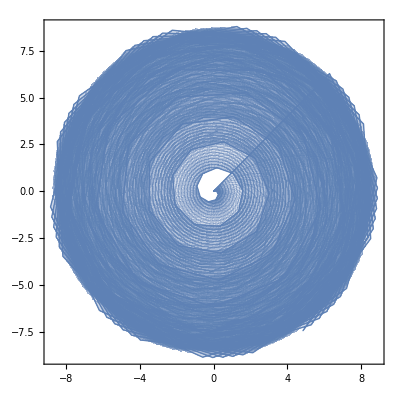

```mathematica
ParametricPlot[
{x Cos[x θ]+x Sin[x θ],x Cos[x θ]-x Sin[x θ]}
,{x,0,2π},{θ,0,2π}
]
```

```mathematica
{x,x}.RotationMatrix[x θ]
```

```mathematica
Manipulate[
ParametricPlot[
{x Cos[x θ]+x Sin[x θ],x Cos[x θ]-x Sin[x θ]}
,{x,0,2π},{θ,0,a}
],{a,0,2π}]
```

ParametricPlot::plld: Endpoints for θ in {θ,0,FE`a$$639} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

```mathematica
{x,x}.RotationMatrix[x]
```

{x Cos[x]+x Sin[x],x Cos[x]-x Sin[x]}

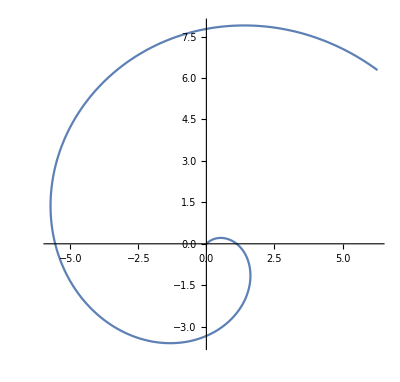

```mathematica
ParametricPlot[
{x Cos[x]+x Sin[x],x Cos[x]-x Sin[x]}
,{x,0,2π}
]
```

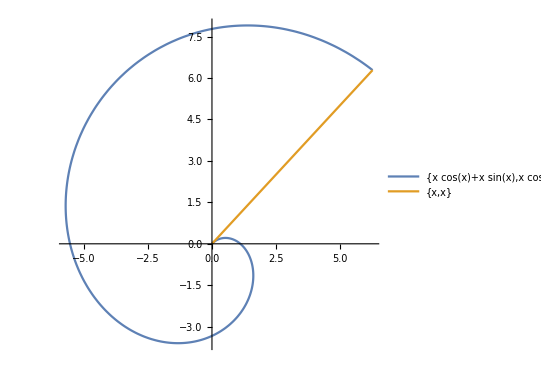

```mathematica
ParametricPlot[{
{x Cos[x]+x Sin[x],x Cos[x]-x Sin[x]},
{x,x}
},{x,0,2π}
,PlotLegends->"Expressions"]
```

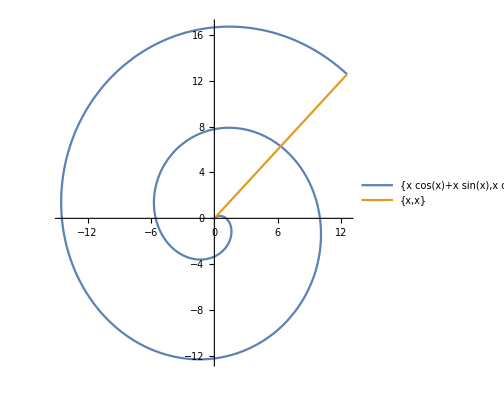

```mathematica
ParametricPlot[{
{x Cos[x]+x Sin[x],x Cos[x]-x Sin[x]},
{x,x}
},{x,0,4π}
,PlotLegends->"Expressions"]
```

```mathematica
Integrate[Norm[D[{x Cos[x]+x Sin[x],x Cos[x]-x Sin[x]},x]],{x,0,4π}]
```

(4 π √(1+16 π^2)+ArcSinh[4 π])/(√2)

```mathematica
N@Out@194
```

114.296

```mathematica
Manipulate[
ParametricPlot3D[
{x Cos[x θ]+x Sin[x θ],x Cos[x θ]-x Sin[x θ],θ}
,{x,0,2π},{θ,0,a}
],{a,0,2π}]
```

ParametricPlot3D::plld: Endpoints for θ in {θ,0,FE`a$$671} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot3D::plld will be suppressed during this calculation.

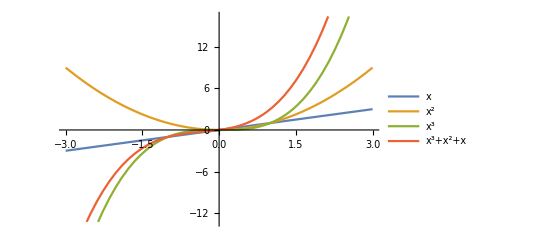

```mathematica
Plot[{x,x^2,x^3,x^3+x^2+x},{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
Map[
{Normalize@{x,#}.Normalize@{x,x},Normalize@{x,#}.Normalize@{x,x^2},Normalize@{x,#}.Normalize@{x,x^3}}
&,{x,x^2,x^3,x^3+x^2+x}]
```

{{x^2/Abs[x]^2,x^2/(√2 Abs[x] √(Abs[x]^2+Abs[x]^4))+x^3/(√2 Abs[x] √(Abs[x]^2+Abs[x]^4)),x^2/(√2 Abs[x] √(Abs[x]^2+Abs[x]^6))+x^4/(√2 Abs[x] √(Abs[x]^2+Abs[x]^6))},{x^2/(√2 Abs[x] √(Abs[x]^2+Abs[x]^4))+x^3/(√2 Abs[x] √(Abs[x]^2+Abs[x]^4)),x^2/(Abs[x]^2+Abs[x]^4)+x^4/(Abs[x]^2+Abs[x]^4),x^2/(√(Abs[x]^2+Abs[x]^4) √(Abs[x]^2+Abs[x]^6))+x^5/(√(Abs[x]^2+Abs[x]^4) √(Abs[x]^2+Abs[x]^6))},{x^2/(√2 Abs[x] √(Abs[x]^2+Abs[x]^6))+x^4/(√2 Abs[x] √(Abs[x]^2+Abs[x]^6)),x^2/(√(Abs[x]^2+Abs[x]^4) √(Abs[x]^2+Abs[x]^6))+x^5/(√(Abs[x]^2+Abs[x]^4) √(Abs[x]^2+Abs[x]^6)),x^2/(Abs[x]^2+Abs[x]^6)+x^6/(Abs[x]^2+Abs[x]^6)},{x^2/(√2 Abs[x] √(Abs[x]^2+Abs[x+x^2+x^3]^2))+(x (x+x^2+x^3))/(√2 Abs[x] √(Abs[x]^2+Abs[x+x^2+x^3]^2)),x^2/(√(Abs[x]^2+Abs[x]^4) √(Abs[x]^2+Abs[x+x^2+x^3]^2))+(x^2 (x+x^2+x^3))/(√(Abs[x]^2+Abs[x]^4) √(Abs[x]^2+Abs[x+x^2+x^3]^2)),x^2/(√(Abs[x]^2+Abs[x]^6) √(Abs[x]^2+Abs[x+x^2+x^3]^2))+(x^3 (x+x^2+x^3))/(√(Abs[x]^2+Abs[x]^6) √(Abs[x]^2+Abs[x+x^2+x^3]^2))}}

```mathematica
Map[
FullSimplify[
{Normalize@{x,#}.Normalize@{x,x},Normalize@{x,#}.Normalize@{x,x^2},Normalize@{x,#}.Normalize@{x,x^3}}
,Element[x,Reals]]
&,{x,x^2,x^3,x^3+x^2+x}]
```

{{1,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4))},{(1+x)/(√2 √(1+x^2)),1,(1+x^3)/(√((1+x^2) (1+x^4)))},{(1+x^2)/(√2 √(1+x^4)),(1+x^3)/(√((1+x^2) (1+x^4))),1},{(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x)))),(1+x)/(√(2+x (2+x))),((1+x^2+x^3+x^4) Abs[x])/(√((1+x^4) (x^2+(x+x^2+x^3)^2)))}}

```mathematica
Flatten[%199]
```

{1,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4)),(1+x)/(√2 √(1+x^2)),1,(1+x^3)/(√((1+x^2) (1+x^4))),(1+x^2)/(√2 √(1+x^4)),(1+x^3)/(√((1+x^2) (1+x^4))),1,(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x)))),(1+x)/(√(2+x (2+x))),((1+x^2+x^3+x^4) Abs[x])/(√((1+x^4) (x^2+(x+x^2+x^3)^2)))}

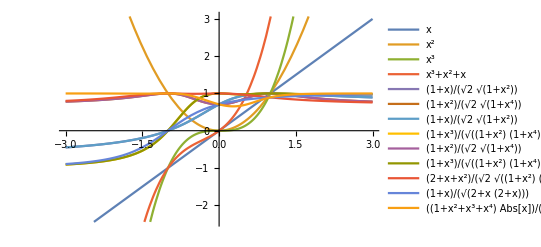

```mathematica
Plot[
{x,x^2,x^3,x^3+x^2+x,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4)),(1+x)/(√2 √(1+x^2)),(1+x^3)/(√((1+x^2) (1+x^4))),(1+x^2)/(√2 √(1+x^4)),(1+x^3)/(√((1+x^2) (1+x^4))),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x)))),(1+x)/(√(2+x (2+x))),((1+x^2+x^3+x^4) Abs[x])/(√((1+x^4) (x^2+(x+x^2+x^3)^2)))}
,{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
Map[
FullSimplify[
Normalize@{x,#}.Normalize@{x,x}
,Element[x,Reals]]
&,{x,x^2,x^3,x^3+x^2+x}]
```

{1,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4)),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))}

```mathematica
{x,x^2,x^3,x^3+x^2+x,1,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4)),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))}
```

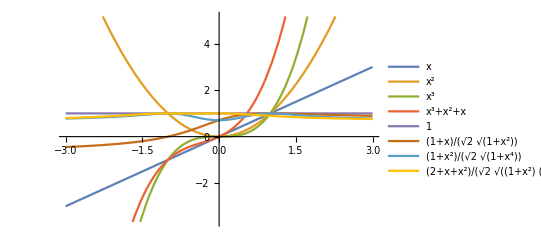

```mathematica
Plot[
{x,x^2,x^3,x^3+x^2+x,1,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4)),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))}
,{x,-3,3},PlotLegends->"Expressions"]
```

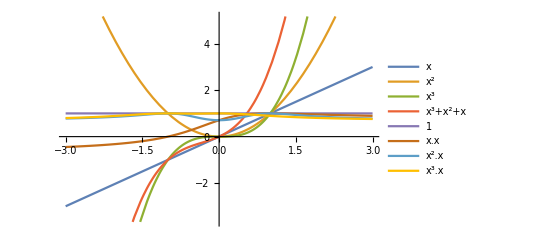

```mathematica
Plot[
{x,x^2,x^3,x^3+x^2+x,1,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4)),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))}
,{x,-3,3},
PlotLegends->{x,x^2,x^3,x^3+x^2+x,1,"x.x","x^2.x","x^3.x","(x^3+x^2+x).x"}]
```

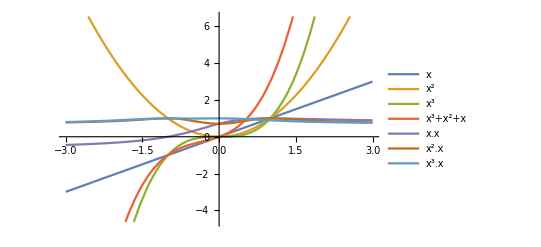

```mathematica
Plot[
{x,x^2,x^3,x^3+x^2+x,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4)),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))}
,{x,-3,3},
PlotLegends->{x,x^2,x^3,x^3+x^2+x,"x.x","x^2.x","x^3.x","(x^3+x^2+x).x"}]
```

```mathematica
Plot[
{x,x^2,x^3,x^3+x^2+x,1,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4)),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))}
,{x,-3,3},
PlotLegends->{x,x^2,x^3,x^3+x^2+x,1,"x.x","x^2.x","x^3.x","(x^3+x^2+x).x"}]
```

-Graphics-

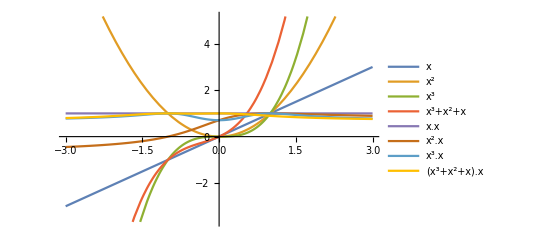

```mathematica
Plot[
{x,x^2,x^3,x^3+x^2+x,1,(1+x)/(√2 √(1+x^2)),(1+x^2)/(√2 √(1+x^4)),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))}
,{x,-3,3},
PlotLegends->{x,x^2,x^3,x^3+x^2+x,"x.x","x^2.x","x^3.x","(x^3+x^2+x).x"}]
```

```mathematica
(1-a[x])p[x]+a[x]q[x]==x^3+x
```

(1-a[x]) p[x]+a[x] q[x]==x+x^3

```mathematica
(1-a[x]) x+a[x] x^3==x+x^3
```

x (1-a[x])+x^3 a[x]==x+x^3

```mathematica
Reduce[x (1-a[x])+x^3 a[x]==x+x^3]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[x (1-a[x])+x^3 a[x]==x+x^3]

```mathematica
Solve[x (1-a[x])+x^3 a[x]==x+x^3,a[x],Reals]
```

{{a[x]→x^3/(-x+x^3)}}

```mathematica
a[x]/.{{a[x]->x^3/(-x+x^3)}}
```

{x^3/(-x+x^3)}

```mathematica
First[{x^3/(-x+x^3)}]
```

x^3/(-x+x^3)

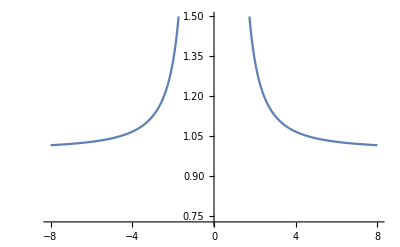

```mathematica
Plot[x^3/(-x+x^3),{x,-8,8}]
```

```mathematica
Plot[x^3/(-x+x^3),{x,-8,8},PlotLegends->"Expressions"]
```

-Graphics-

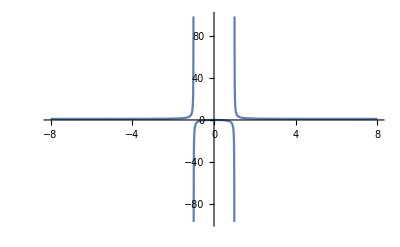

```mathematica
Plot[x^3/(-x+x^3),{x,-8,8},PlotRange->Full]
```

```mathematica
Sinc[x]
```

Sinc[x]

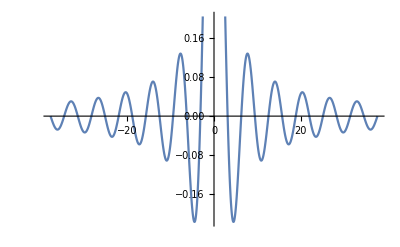

```mathematica
Plot[Sinc[x],{x,-37.69911184307752,37.69911184307752}]
```

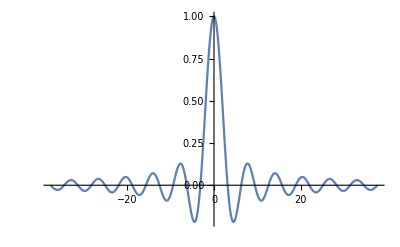

```mathematica
Plot[Sinc[x],{x,-37.69911184307752,37.69911184307752},PlotRange->Full]
```

```mathematica
(1-Sinc[x])x^3+Sinc[x]x
```

x^3 (1-Sinc[x])+x Sinc[x]

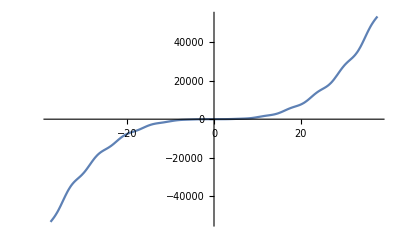

```mathematica
Plot[x^3 (1-Sinc[x])+x Sinc[x],{x,-37.69911184307752,37.69911184307752}]
```

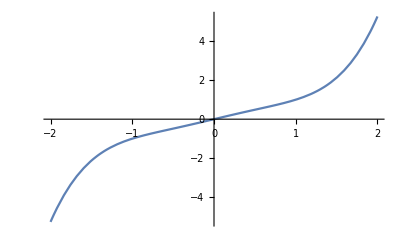

```mathematica
Plot[x^3 (1-Sinc[x])+x Sinc[x],{x,-2,2}]
```

```mathematica
FindRoot[x^2-x-1,{x}]
```

FindRoot::srect: Value x in search specification {x} is not a number or array of numbers.

FindRoot[x^2-x-1,{x}]

```mathematica
FindRoot[x^2-x-1,x]
```

FindRoot::fdss: Search specification x should be a list with 1 to 5 elements.

FindRoot[x^2-x-1,x]

```mathematica
-x^2
```

-x^2

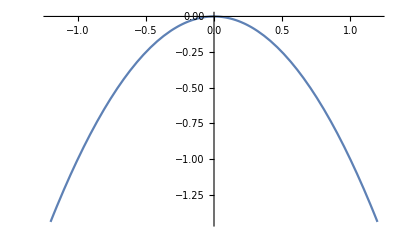

```mathematica
Plot[-x^2,{x,-1.2,1.2}]
```

```mathematica
-x^2+1
```

1-x^2

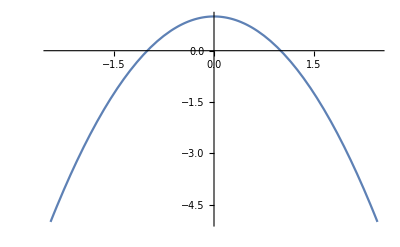

```mathematica
Plot[1-x^2,{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
Manipulate[
Plot[(1-a)1-x^2+a Cos[x],{x,-2,2}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[(1-a)(1-x^2)+a Cos[x],{x,-2,2}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[(1-a)(1-x^2)+a Cos[x],{x,-2π,2π}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[(1-a)(1-x^2)+a Cos[x],{x,-20π,20π}]
,{a,0,1}]
```

```mathematica
Normalize@{1,f'[x]}.(Normalize@{1,1}.RotationMatrix[θ])
```

(Cos[θ]/(√2)+Sin[θ]/(√2))/(√(1+Abs[f'[x]]^2))+((Cos[θ]/(√2)-Sin[θ]/(√2)) f'[x])/(√(1+Abs[f'[x]]^2))

```mathematica
FullSimplify[
Normalize@{1,f'[x]}.(Normalize@{1,1}.RotationMatrix[θ])
,{f'[x],θ}∈Reals]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))

```mathematica
With[{f=Sinc},(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))]
```

(Cos[θ]+(Cos[x]/x-Sin[x]/x^2) (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+(Cos[x]/x-Sin[x]/x^2)^2))

```mathematica
Manipulate[Plot[(Cos[θ]+(Cos[x]/x-Sin[x]/x^2) (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+(Cos[x]/x-Sin[x]/x^2)^2)),{x,-1.1707574776968341,1.1707574776968341}],{θ,-4.600996821166785,4.600996821166785}]
```

```mathematica
Plot3D[(Cos[θ]+(Cos[x]/x-Sin[x]/x^2) (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+(Cos[x]/x-Sin[x]/x^2)^2))
,{x,-10,10},{θ,0,2π}]
```

-Graphics3D-

```mathematica
L[x,θ,y,y']
```

L[x,θ,y,y']

```mathematica
Div[f[x,θ],{x,θ}]
```

Div::sclr: The scalar expression f[x,θ] does not have a divergence.

f[x,θ]{x,θ}

```mathematica
Div[{f[x,θ]},{x,θ}]
```

Div::ndimv: There is no 2-dimensional divergence for the 1-dimensional vector {f[x,θ]}.

{f[x,θ]}{x,θ}

```mathematica
y==3
```

y==3

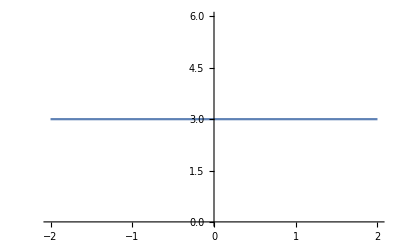

```mathematica
Plot[3,{x,-2,2}]
```

```mathematica
FullSimplify[
Normalize@{x,3}.Normalize@{x,f[x]}
,{x,f[x]}∈Reals]
```

(x^2+3 f[x])/(√((9+x^2) (x^2+f[x]^2)))

```mathematica
With[{f=x^2},(x^2+3 f[x])/(√((9+x^2) (x^2+f[x]^2)))]
```

(x^2+3 x^2[x])/(√((9+x^2) (x^2+(x^2[x])^2)))

```mathematica
With[{f=Function[x,x^2]},(x^2+3 f[x])/(√((9+x^2) (x^2+f[x]^2)))]
```

(4 x^2)/(√((9+x^2) (x^2+x^4)))

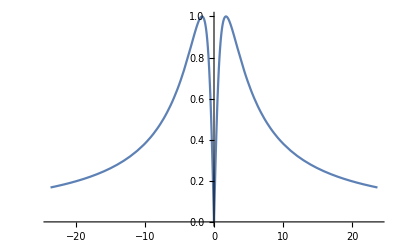

```mathematica
Plot[(4 x^2)/(√((9+x^2) (x^2+x^4))),{x,-23.66,23.66}]
```

```mathematica
FullSimplify[
With[{f=Function[x,x x]},
Normalize@{x,3}.Normalize@{x,f[x]}
],{x,f[x]}∈Reals]
```

(4 Abs[x])/(√((1+x^2) (9+x^2)))

```mathematica
FullSimplify[
With[{f=Function[x,x x]},
Normalize@{x,a}.Normalize@{x,f[x]}
],{x,a,f[x]}∈Reals]
```

((1+a) x^2)/(√((a^2+x^2) (x^2+x^4)))

```mathematica
FullSimplify[
With[{f=Function[x,x x x- x x -x +1]},
Normalize@{x,a}.Normalize@{x,f[x]}
],{x,a,f[x]}∈Reals]
```

(x^2+a (-1+x)^2 (1+x))/(√((a^2+x^2) (x^2+(-1+x)^4 (1+x)^2)))

```mathematica
Manipulate[
Plot[{
FullSimplify[
With[{f=Function[x,x x x- x x -x +1]},
Normalize@{x,a}.Normalize@{x,f[x]}
],{x,a,f[x]}∈Reals],
a,
x x x- x x -x +1
},{x,-3,3}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[{
FullSimplify[
With[{f=Function[x,x x x- x x -x +1]},
Normalize@{x,a}.Normalize@{x,f[x]}
],{x,a,f[x]}∈Reals],
a,
x x x- x x -x +1
},{x,-3,3}]
,{a,-3,3}]
```

```mathematica
Manipulate[
Plot[{
FullSimplify[
With[{f=Function[x,x x x- x x -x +1]},
Normalize@{x,a}.Normalize@{x,f[x]}
],{x,a,f[x]}∈Reals],
a,
x x x- x x -x +1
},{x,-3,3},PlotRange->{-5,5}]
,{a,-3,3}]
```

```mathematica
FullSimplify[
Normalize@{x,0}.Normalize@{x,f[x]}
,{x,f[x]}∈Reals]
```

Abs[x]/(√(x^2+f[x]^2))

```mathematica
With[{f=Function[x,x x x- x x -x +1]},Abs[x]/(√(x^2+f[x]^2))]
```

Abs[x]/(√(x^2+(1-x-x^2+x^3)^2))

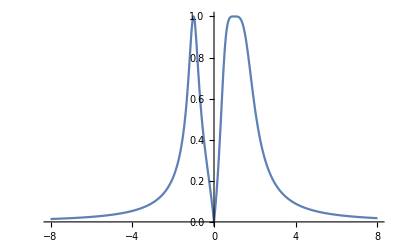

```mathematica
Plot[Abs[x]/(√(x^2+(1-x-x^2+x^3)^2)),{x,-8,8}]
```

```mathematica
x x x- x x -x +1
```

1-x-x^2+x^3

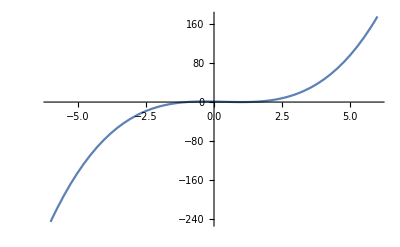

```mathematica
Plot[1-x-x^2+x^3,{x,-6.,6.}]
```

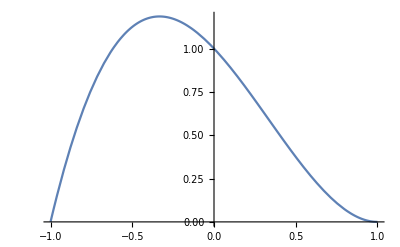

```mathematica
Plot[1-x-x^2+x^3,{x,-1,1}]
```

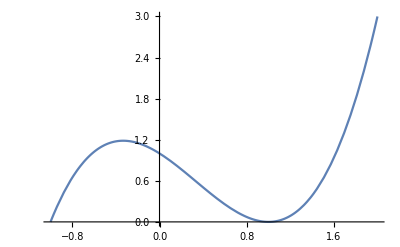

```mathematica
Plot[1-x-x^2+x^3,{x,-1,2}]
```

```mathematica
Abs[x]/(√(x^2+(1-x-x^2+x^3)^2))==1
```

Abs[x]/(√(x^2+(1-x-x^2+x^3)^2))==1

```mathematica
Reduce[Abs[x]/(√(x^2+(1-x-x^2+x^3)^2))==1]
```

x==-1||x==1||x==ⅈ Root-0.0716Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{1,3}]-0.0715896438871492+Root-0.933Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,1]-0.9333540846193363||x==ⅈ Root0.0716Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{1,4}]0.0715896438871492+Root-0.933Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,1]-0.9333540846193363||x==ⅈ Root-0.195Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{2,1}]-0.19476243933619147+Root0.487Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,2]0.48673143358591325||x==ⅈ Root0.195Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{2,2}]0.19476243933619147+Root0.487Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,2]0.48673143358591325||x==ⅈ Root-0.709Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{3,2}]-0.7086188733646399+Root1.31Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,3]1.3144500450939367||x==ⅈ Root0.709Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{3,5}]0.7086188733646399+Root1.31Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,3]1.3144500450939367

```mathematica
Reduce[Abs[x]/(√(x^2+(1-x-x^2+x^3)^2))==1,x,Reals]
```

x==-1||x==1

```mathematica
Abs[x]==√(x^2+(1-x-x^2+x^3)^2)
```

Abs[x]==√(x^2+(1-x-x^2+x^3)^2)

```mathematica
Reduce[Abs[x]==√(x^2+(1-x-x^2+x^3)^2)]
```

x==-1||x==1||x==ⅈ Root-0.0716Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{1,3}]-0.0715896438871492+Root-0.933Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,1]-0.9333540846193363||x==ⅈ Root0.0716Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{1,4}]0.0715896438871492+Root-0.933Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,1]-0.9333540846193363||x==ⅈ Root-0.195Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{2,1}]-0.19476243933619147+Root0.487Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,2]0.48673143358591325||x==ⅈ Root0.195Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{2,2}]0.19476243933619147+Root0.487Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,2]0.48673143358591325||x==ⅈ Root-0.709Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{3,2}]-0.7086188733646399+Root1.31Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,3]1.3144500450939367||x==ⅈ Root0.709Root[{4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,-1+2 #1+#1^2-4 #1^3+#1^4+2 #1^5-#1^6+#2^2+12 #1 #2^2-6 #1^2 #2^2-20 #1^3 #2^2+15 #1^4 #2^2+#2^4+10 #1 #2^4-15 #1^2 #2^4+#2^6&},{3,5}]0.7086188733646399+Root1.31Root[4-16 #1-36 #1^2+255 #1^3-108 #1^4-1116 #1^5+1808 #1^6+192 #1^7-256 #1^8-13312 #1^9+31488 #1^10-18944 #1^11-20480 #1^12+36864 #1^13-20480 #1^14+4096 #1^15&,3]1.3144500450939367

```mathematica
√(x^2+(1-x-x^2+x^3)^2)
```

√(x^2+(1-x-x^2+x^3)^2)

```mathematica
Plot[√(x^2+(1-x-x^2+x^3)^2),{x,-15.689298384413611,15.251377969928505}]
```

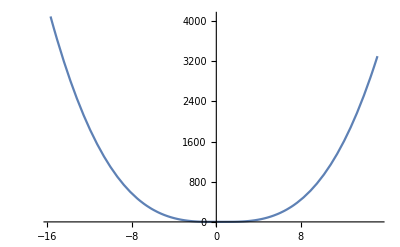
```mathematica
-Graphics-251377969928505
```

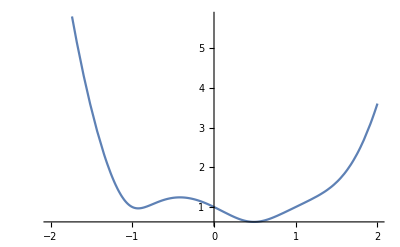

```mathematica
Plot[√(x^2+(1-x-x^2+x^3)^2),{x,-2,2}]
```

```mathematica
Abs[x]/(√(x^2+f[x]^2))==1
```

Abs[x]/(√(x^2+f[x]^2))==1

```mathematica
Reduce[Abs[x]/(√(x^2+f[x]^2))==1]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Abs[x]/(√(x^2+f[x]^2))==1]

```mathematica
Abs[x]==√(x^2+f[x]^2)
```

Abs[x]==√(x^2+f[x]^2)

```mathematica
Reduce[Abs[x]==√(x^2+f[x]^2)]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Abs[x]==√(x^2+f[x]^2)]

```mathematica
Reduce[Abs[x]==√(x^2+f[x]^2),f[x],Reals]
```

f[x]==0

```mathematica
x^2==x^2+f[x]^2
```

x^2==x^2+f[x]^2

```mathematica
Reduce[x^2==x^2+f[x]^2]
```

f[x]==0

```mathematica
D[Sinc[x],{x,2}]
```

-(2 Cos[x])/x^2+(2 Sin[x])/x^3-Sin[x]/x

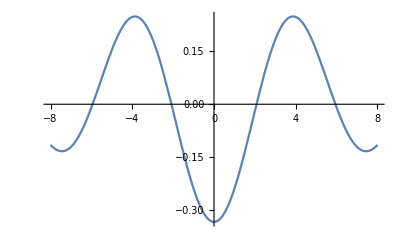

```mathematica
Plot[-(2 Cos[x])/x^2+(2 Sin[x])/x^3-Sin[x]/x,{x,-8,8}]
```

```mathematica
{x==r Cos[θ],y==r Sin[θ]}
```

{x==r Cos[θ],y==r Sin[θ]}

```mathematica
√((r Cos[θ])^2+(r Sin[θ])^2)
```

√(r^2 Cos[θ]^2+r^2 Sin[θ]^2)

```mathematica
Plot3D[√(r^2 Cos[θ]^2+r^2 Sin[θ]^2),{r,-2.337486238896889,2.337486238896889},{θ,-2.470278535103651,2.470278535103651}]
```

-Graphics3D-

```mathematica
f@*g
```

f@*g

```mathematica
(f@*g)[x]
```

f[g[x]]

```mathematica
InverseFunction@(f@*g)
```

g^(-1)@*f^(-1)

```mathematica
InverseFunction@(f@*g)==g^(-1)@*f^(-1)
```

True

```mathematica
∞/0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
FullForm[ComplexInfinity]
```

DirectedInfinity[]

```mathematica
g[f[x]]==λ f[x]
```

g[f[x]]==λ f[x]

```mathematica
Reduce[g[f[x]]==λ f[x]]
```

(g[0]==0&&f[x]==0)||((Re[f[x]]<0||(Re[f[x]]==0&&(Im[f[x]]<0||Im[f[x]]>0))||Re[f[x]]>0)&&λ==g[f[x]]/f[x])

```mathematica
Solve[g[f[x]]==λ f[x],λ,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[g[f[x]]==λ f[x],λ,ℝ]

```mathematica
g[f[x]]/λ==f[x]
```

g[f[x]]/λ==f[x]

```mathematica
Manipulate[
Plot[{
FullSimplify[
With[{f=Function[x,x x x- x x -x +1]},
Normalize@{x,0}.Normalize@{x,f[x]}
],{x,a,f[x]}∈Reals],
a,
x x x- x x -x +1
},{x,-3,3},PlotRange->{-5,5}]
,{a,-3,3}]
```

```mathematica
FullSimplify[
Normalize@{1,f'[x]}.(Normalize@{1,1}.RotationMatrix[θ])
,{f'[x],θ}∈Reals]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))

```mathematica
With[{f=Identity},Out[292]]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))

```mathematica
With[{f=Identity},(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))]
```

Cos[θ]

```mathematica
With[{f=Cos},Out[292]]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))

```mathematica
With[{f=Cos},(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))]
```

(Cos[θ]-Sin[x] (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+Sin[x]^2))

```mathematica
Manipulate[Plot[(Cos[θ]-Sin[x] (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+Sin[x]^2)),{x,-1.1428409216290751,1.8789682773232774}],{θ,0,2π}]
```

```mathematica
Plot3D[(Cos[θ]-Sin[x] (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+Sin[x]^2)),{x,-10,10},{θ,0,2π}]
```

-Graphics3D-

```mathematica
With[{f=Function[x,x x x- x x -x +1]},Abs[x]/(√(x^2+f[x]^2))]
```

Abs[x]/(√(x^2+(1-x-x^2+x^3)^2))

```mathematica
Plot[Abs[x]/(√(x^2+(1-x-x^2+x^3)^2)),{x,-8,8}]
```

-Graphics-

```mathematica
With[{f=Function[x,x x x- x x -x]},Abs[x]/(√(x^2+f[x]^2))]
```

Abs[x]/(√(x^2+(-x-x^2+x^3)^2))

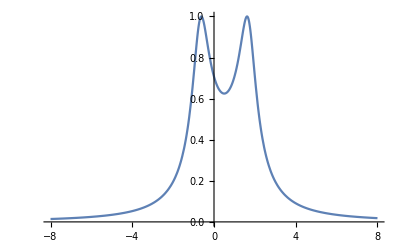

```mathematica
Plot[Abs[x]/(√(x^2+(-x-x^2+x^3)^2)),{x,-8,8}]
```

```mathematica
Solve[x x x- x x -x,x,Reals]
```

Solve::naqs: -x-x^2+x^3 is not a quantified system of equations and inequalities.

Solve[-x-x^2+x^3,x,ℝ]

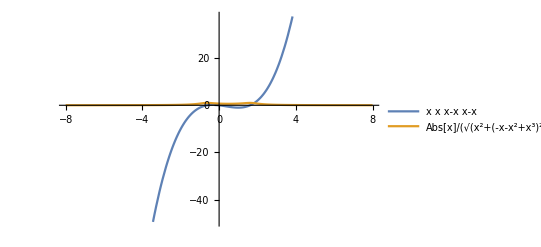

```mathematica
Plot[{x x x- x x -x,Abs[x]/(√(x^2+(-x-x^2+x^3)^2))},{x,-8,8},PlotLegends->"Expressions",ImageSize->Full]
```

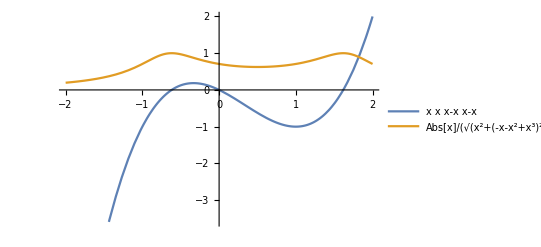

```mathematica
Plot[{x x x- x x -x,Abs[x]/(√(x^2+(-x-x^2+x^3)^2))},{x,-2,2},PlotLegends->"Expressions",ImageSize->Full]
```

```mathematica
Abs[x]/(√(x^2+(-x-x^2+x^3)^2))==1
```

Abs[x]/(√(x^2+(-x-x^2+x^3)^2))==1

```mathematica
Reduce[Abs[x]/(√(x^2+(-x-x^2+x^3)^2))==1]
```

$Aborted

```mathematica
Reduce[Abs[x]/(√(x^2+(-x-x^2+x^3)^2))==1,x,Reals]
```

x==1/2 (1-√5)||x==1/2 (1+√5)

```mathematica
x x x- x x -x/.x->1/2 (1+√5)
```

1/2 (-1-√5)-1/4 (1+√5)^2+1/8 (1+√5)^3

```mathematica
N[1/2 (-1-√5)-1/4 (1+√5)^2+1/8 (1+√5)^3]
```

0.

```mathematica
x x x- x x -x/.x->1/2 (1-√5)
```

-1/4 (1-√5)^2+1/8 (1-√5)^3+1/2 (-1+√5)

```mathematica
IsolatingInterval[-1/4 (1-√5)^2+1/8 (1-√5)^3+1/2 (-1+√5)]
```

{0,0}

```mathematica
RootReduce[-1/4 (1-√5)^2+1/8 (1-√5)^3+1/2 (-1+√5)]
```

0

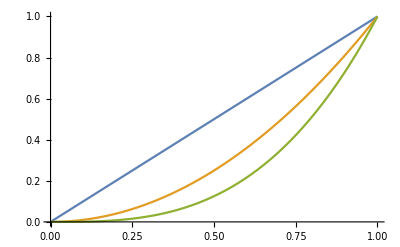

```mathematica
Plot[{x,x^2,x^3},{x,0,1}]
```

```mathematica
Composition[a,b,c]
```

a@*b@*c

```mathematica
InverseFunction[Composition[a,b,c]]
```

c^(-1)@*b^(-1)@*a^(-1)

```mathematica
Composition[InverseFunction[Composition[a,b,c]],Composition[a,b,c]][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction::ifun will be suppressed during this calculation.

x

```mathematica
Composition[InverseFunction[f],f]
```

f^(-1)@*f

```mathematica
Composition[InverseFunction[f],f]==Composition[Identity]==Identity
```

f^(-1)@*f==Identity==Identity

```mathematica
Composition[InverseFunction[f],f][x]==Composition[Identity][x]==Identity[x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

True

```mathematica
Apply[Composition,{a,b}]
```

a@*b

```mathematica
Composition[Composition[a],b,c]==Composition[a,Composition[b,c]]
```

True

```mathematica
Composition[Composition[a],b,c]
```

a@*b@*c

```mathematica
Composition[a,Composition[b,c]]
```

a@*b@*c

```mathematica
Dt@Composition[a,b,c]
```

Dt[c] Composition^(0,0,1)[a,b,c]+Dt[b] Composition^(0,1,0)[a,b,c]+Dt[a] Composition^(1,0,0)[a,b,c]

```mathematica
Dt@Composition[a,b,c][x]
```

Dt[x] a'[b[c[x]]] b'[c[x]] c'[x]

```mathematica
Dt[Composition[a,b,c][x]]
```

Dt[x] a'[b[c[x]]] b'[c[x]] c'[x]

```mathematica
Dt[f[x]==f[x-α]+f[α]]
```

Dt[x] f'[x]==(Dt[x]-Dt[α]) f'[x-α]+Dt[α] f'[α]

```mathematica
ExpandAll[Dt[x] f'[x]==(Dt[x]-Dt[α]) f'[x-α]+Dt[α] f'[α]]
```

Dt[x] f'[x]==Dt[x] f'[x-α]-Dt[α] f'[x-α]+Dt[α] f'[α]

```mathematica
Dt[f[x+a]==f[x]+∫_x^(x+a) f'[x]ⅆx]
```

True

```mathematica
Dt[f[x]+∫_x^(x+a) f'[x]ⅆx]
```

(Dt[a]+Dt[x]) f'[a+x]

```mathematica
Dt[f[x+a]]
```

(Dt[a]+Dt[x]) f'[a+x]

```mathematica
Dt[f[x+a,y]]
```

Dt[y] f^(0,1)[a+x,y]+(Dt[a]+Dt[x]) f^(1,0)[a+x,y]

```mathematica
Dt[f[x+a,y+b]]
```

(Dt[b]+Dt[y]) f^(0,1)[a+x,b+y]+(Dt[a]+Dt[x]) f^(1,0)[a+x,b+y]

```mathematica
Dt[D[f[x],x]==λ f[x]]
```

Dt[x] f''[x]==Dt[λ] f[x]+λ Dt[x] f'[x]

```mathematica
2+3
```

5

```mathematica
Solve[2+a==λ 2,λ,Reals]
```

{{λ→1+a/2}}

```mathematica
Solve[b+a==λ a,λ,Reals]
```

{{λ→-(-a-b)/a}}

```mathematica
1/(√((x^2+y^2)^2))
```

1/(√((x^2+y^2)^2))

```mathematica
Plot3D[1/(√((x^2+y^2)^2)),{x,-1.9201127362509969,1.9201127362509969},{y,-1.9201127362509969,1.9201127362509969}]
```

-Graphics3D-

```mathematica
Plot3D[1/(√((x^2+y^2)^2)),{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[1/(√((x^2+y^2)^2)),{x,y}∈Disk[],PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[1/(√((x^2+y^2)^2)),{x,y}∈Disk[]]
```

-Graphics3D-

Power::infy: Infinite expression 1/0. encountered.

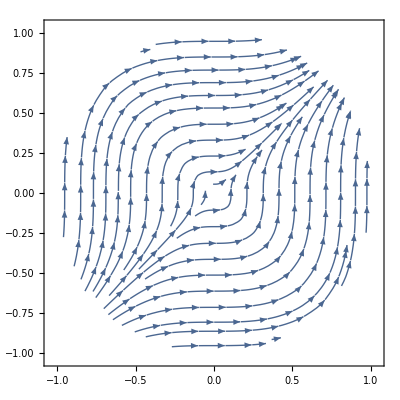

```mathematica
StreamPlot[
{1/x^2,1/y^2}
,{x,y}∈Disk[]]
```

```mathematica
{x,1/(√((x^2+y^2)^2))}
```

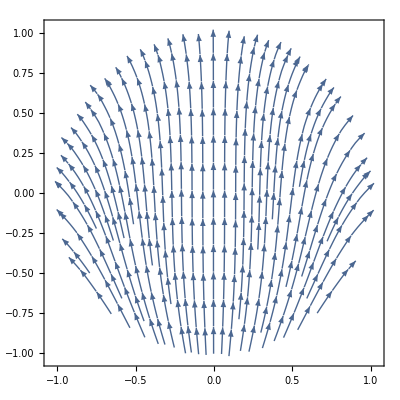

```mathematica
StreamPlot[
{x,1/(√((x^2+y^2)^2))}
,{x,y}∈Disk[]]
```

```mathematica
Curl[{x,y},{x,y}]
```

0

```mathematica
Curl[1/(√((x^2+y^2)^2)),{x,y}]
```

{(2 y (x^2+y^2))/(((x^2+y^2)^2)^(3/2)),-(2 x (x^2+y^2))/(((x^2+y^2)^2)^(3/2))}

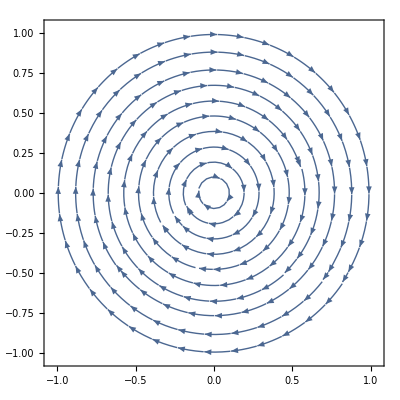

```mathematica
StreamPlot[
{(2 y (x^2+y^2))/(((x^2+y^2)^2)^(3/2)),-(2 x (x^2+y^2))/(((x^2+y^2)^2)^(3/2))}
,{x,y}∈Disk[]]
```

```mathematica
Div[1/(√((x^2+y^2)^2)),{x,y}]
```

Div::sclr: The scalar expression 1/(√((x^2+y^2)^2)) does not have a divergence.

1/(√((x^2+y^2)^2)){x,y}

```mathematica
Grad[1/(√((x^2+y^2)^2)),{x,y}]
```

{-(2 x (x^2+y^2))/(((x^2+y^2)^2)^(3/2)),-(2 y (x^2+y^2))/(((x^2+y^2)^2)^(3/2))}

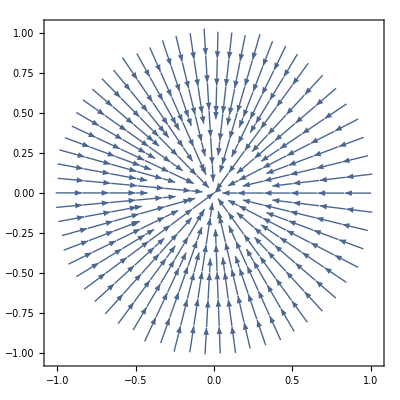

```mathematica
StreamPlot[
{-(2 x (x^2+y^2))/(((x^2+y^2)^2)^(3/2)),-(2 y (x^2+y^2))/(((x^2+y^2)^2)^(3/2))}
,{x,y}∈Disk[]]
```

```mathematica
{(2 y (x^2+y^2))/(((x^2+y^2)^2)^(3/2)),-(2 x (x^2+y^2))/(((x^2+y^2)^2)^(3/2))}
```

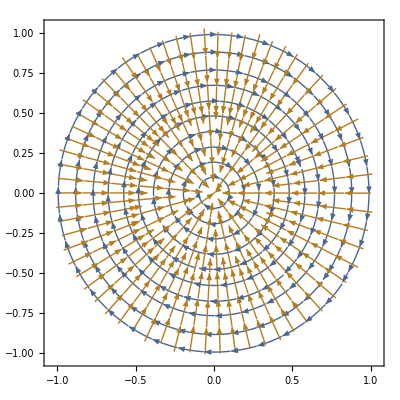

```mathematica
StreamPlot[{
{(2 y (x^2+y^2))/(((x^2+y^2)^2)^(3/2)),-(2 x (x^2+y^2))/(((x^2+y^2)^2)^(3/2))},
{-(2 x (x^2+y^2))/(((x^2+y^2)^2)^(3/2)),-(2 y (x^2+y^2))/(((x^2+y^2)^2)^(3/2))}
},{x,y}∈Disk[]]
```

```mathematica
Plot3D[(Cos[θ]+(Cos[x]/x-Sin[x]/x^2) (Cos[θ]-Sin[θ])+Sin[θ])/(√2 √(1+(Cos[x]/x-Sin[x]/x^2)^2))
,{x,-10,10},{θ,0,2π}]
```

-Graphics3D-

```mathematica
FullSimplify[
With[{f=Function[x, x x]},
Normalize@{1,f'[x]}.(Normalize@{1,1}.RotationMatrix[θ])
],x∈Reals]
```

(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2))

```mathematica
Manipulate[Plot[(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),{x,-1.2170805184051374,2.7927094136263095}],{θ,-4.519261154946495,1.1325382529043913}]
```

```mathematica
Plot3D[(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),{x,θ}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),{x,θ}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Plot3D[(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),{x,-3,3},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),{x,-5,5},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Grad[(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),{x,θ}]
```

{(2 Cos[θ]-2 Sin[θ])/(√(2+8 x^2))-(8 x (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(3/2)),(Cos[θ]-2 x Cos[θ]-Sin[θ]-2 x Sin[θ])/(√(2+8 x^2))}

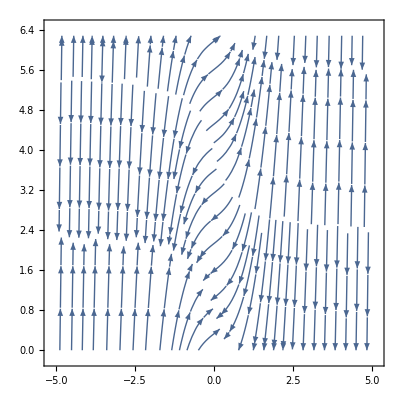

```mathematica
StreamPlot[{
{(2 Cos[θ]-2 Sin[θ])/(√(2+8 x^2))-(8 x (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(3/2)),(Cos[θ]-2 x Cos[θ]-Sin[θ]-2 x Sin[θ])/(√(2+8 x^2))},
},{x,-5,5},{θ,0,2π}]
```

```mathematica
Div[(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),{x,θ}]
```

Div::sclr: The scalar expression (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)) does not have a divergence.

(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)){x,θ}

```mathematica
Div[{(2 Cos[θ]-2 Sin[θ])/(√(2+8 x^2))-(8 x (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(3/2)),(Cos[θ]-2 x Cos[θ]-Sin[θ]-2 x Sin[θ])/(√(2+8 x^2))},{x,θ}]
```

-(16 x (2 Cos[θ]-2 Sin[θ]))/((2+8 x^2)^(3/2))+(192 x^2 (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(5/2))-(8 (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(3/2))+(-Cos[θ]-2 x Cos[θ]-Sin[θ]+2 x Sin[θ])/(√(2+8 x^2))

```mathematica
Manipulate[Plot[%366,{x,-3.369226922143049,3.369226922143049}],{θ,-5.9256954863315325,4.276261036497223}]
```

```mathematica
Plot3D[-(16 x (2 Cos[θ]-2 Sin[θ]))/((2+8 x^2)^(3/2))+(192 x^2 (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(5/2))-(8 (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(3/2))+(-Cos[θ]-2 x Cos[θ]-Sin[θ]+2 x Sin[θ])/(√(2+8 x^2)),{x,-5,5},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Curl[(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),{x,θ}]
```

{-(Cos[θ]-2 x Cos[θ]-Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),(2 Cos[θ]-2 Sin[θ])/(√(2+8 x^2))-(8 x (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(3/2))}

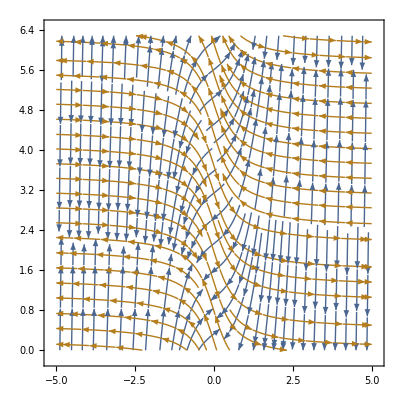

```mathematica
StreamPlot[{
{(2 Cos[θ]-2 Sin[θ])/(√(2+8 x^2))-(8 x (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(3/2)),(Cos[θ]-2 x Cos[θ]-Sin[θ]-2 x Sin[θ])/(√(2+8 x^2))},
{-(Cos[θ]-2 x Cos[θ]-Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),(2 Cos[θ]-2 Sin[θ])/(√(2+8 x^2))-(8 x (Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ]))/((2+8 x^2)^(3/2))}
},{x,-5,5},{θ,0,2π}]
```

```mathematica
Grad[{x[a,b],y[a,b]},{a,b}]
```

{{x^(1,0)[a,b],x^(0,1)[a,b]},{y^(1,0)[a,b],y^(0,1)[a,b]}}

```mathematica
Grad[f[a,b],{a,b}]
```

{f^(1,0)[a,b],f^(0,1)[a,b]}

```mathematica
Normalize@Grad[f[a,b],{a,b}]
```

{(f^(1,0)[a,b])/(√(Abs[f^(0,1)[a,b]]^2+Abs[f^(1,0)[a,b]]^2)),(f^(0,1)[a,b])/(√(Abs[f^(0,1)[a,b]]^2+Abs[f^(1,0)[a,b]]^2))}

```mathematica
Normalize@Grad[f[a,b],{a,b}].Normalize@Curl[f[a,b],{a,b}]
```

0

```mathematica
Grad[f[a,b],{a,b}].Curl[f[a,b],{a,b}]
```

0

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
SurfaceData["Sphere","AlgebraicEquation"]
```

Function[a,Function[{x,y,z},x^2+y^2+z^2-a^2]]

```mathematica
SurfaceData["Sphere","ParametricEquations"]
```

Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][1][θ,ϕ]
```

{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}

```mathematica
ParametricPlot3D[
{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}
,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]},
{Cos[θ],Sin[ϕ],0}
},{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]},
{Cos[θ],Sin[θ],0}
},{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
(1-a)p+a q/.{p->{Cos[θ],Sin[θ],0},q->{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}}
```

{(1-a) Cos[θ]+a Cos[θ] Sin[ϕ],(1-a) Sin[θ]+a Sin[θ] Sin[ϕ],a Cos[ϕ]}

```mathematica
Manipulate[
ParametricPlot3D[{
{(1-a) Cos[θ]+a Cos[θ] Sin[ϕ],(1-a) Sin[θ]+a Sin[θ] Sin[ϕ],a Cos[ϕ]}
},{θ,0,2π},{ϕ,0,2π}]
,{a,0,1}]
```

```mathematica
{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}/.{θ->a,ϕ->b}
```

{Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}

```mathematica
{Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}/.{\}
```

```mathematica
{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}/.{θ->c,ϕ->d}
```

{Cos[c] Sin[d],Sin[c] Sin[d],Cos[d]}

```mathematica
Normalize@{Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}.Normalize@{Cos[c] Sin[d],Sin[c] Sin[d],Cos[d]}
```

(Cos[b] Cos[d])/(√(Abs[Cos[b]]^2+Abs[Cos[a] Sin[b]]^2+Abs[Sin[a] Sin[b]]^2) √(Abs[Cos[d]]^2+Abs[Cos[c] Sin[d]]^2+Abs[Sin[c] Sin[d]]^2))+(Cos[a] Cos[c] Sin[b] Sin[d])/(√(Abs[Cos[b]]^2+Abs[Cos[a] Sin[b]]^2+Abs[Sin[a] Sin[b]]^2) √(Abs[Cos[d]]^2+Abs[Cos[c] Sin[d]]^2+Abs[Sin[c] Sin[d]]^2))+(Sin[a] Sin[b] Sin[c] Sin[d])/(√(Abs[Cos[b]]^2+Abs[Cos[a] Sin[b]]^2+Abs[Sin[a] Sin[b]]^2) √(Abs[Cos[d]]^2+Abs[Cos[c] Sin[d]]^2+Abs[Sin[c] Sin[d]]^2))

```mathematica
FullSimplify[
Normalize@{Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}.Normalize@{Cos[c] Sin[d],Sin[c] Sin[d],Cos[d]}
,{a,b,c,d}∈Reals]
```

Cos[b] Cos[d]+Cos[a-c] Sin[b] Sin[d]

```mathematica
{Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[c] Sin[d],Sin[c] Sin[d],Cos[d]}
```

{Cos[a] Sin[b]-Cos[c] Sin[d],Sin[a] Sin[b]-Sin[c] Sin[d],Cos[b]-Cos[d]}

```mathematica
FullSimplify[
Normalize@{Cos[a] Sin[b]-Cos[c] Sin[d],Sin[a] Sin[b]-Sin[c] Sin[d],Cos[b]-Cos[d]}
,{a,b,c,d}∈Reals]
```

{(Cos[a] Sin[b]-Cos[c] Sin[d])/(√2 √(1-Cos[b] Cos[d]-Cos[a-c] Sin[b] Sin[d])),(Sin[a] Sin[b]-Sin[c] Sin[d])/(√2 √(1-Cos[b] Cos[d]-Cos[a-c] Sin[b] Sin[d])),(Cos[b]-Cos[d])/(√2 √(1-Cos[b] Cos[d]-Cos[a-c] Sin[b] Sin[d]))}

```mathematica
{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}
```

```mathematica
FullSimplify[
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]})
,{a,b,θ,ϕ}∈Reals]
```

{(Cos[a] Sin[b]-Cos[θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Sin[a] Sin[b]-Sin[θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Cos[b]-Cos[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ]))}

```mathematica
FullSimplify[
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]})
,{a,b,θ,ϕ}∈Reals]
```

```mathematica
ContourPlot3D[x^2+y^2+z^2==1,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
x^2+y^2+z^2
```

x^2+y^2+z^2

```mathematica
(x^2+y^2+z^2){x,y,z}
```

{2 x,2 y,2 z}

```mathematica
VectorPlot3D[
{2 x,2 y,2 z},
{x,y,z}∈Sphere[]]
```

VectorPlot3D::idomdim: {x,y,z}∈Sphere[] does not have a valid dimension as a plotting domain.

VectorPlot3D[{2 x,2 y,2 z},{x,y,z}∈Sphere[]]

```mathematica
VectorPlot3D[
{2 x,2 y,2 z},
{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
{2 (Sin[θ]Cos[ϕ]),2 Sin[θ]Sin[ϕ],2 Cos[θ]}
```

{2 Cos[ϕ] Sin[θ],2 Sin[θ] Sin[ϕ],2 Cos[θ]}

```mathematica
VectorPlot3D[
{2 x,2 y,2 z},
{x,-1,1},{y,-1,1},{z,-1,1}]
```

```mathematica
{2 Cos[ϕ] Sin[θ],2 Sin[θ] Sin[ϕ],2 Cos[θ]}
```

```mathematica
VectorPlot3D[
{2 x,2 y,2 z},
{x,-1,1},{y,-1,1}]
```

```mathematica
ParametricPlot3D[
{2 Cos[ϕ] Sin[θ],2 Sin[θ] Sin[ϕ],2 Cos[θ]}
,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]}
,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
Curl[{Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]},{θ,ϕ}]
```

Curl::ndimv: There is no 2-dimensional curl for the 3-dimensional vector {Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}{θ,ϕ}

```mathematica
Div[{Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]},{θ,ϕ}]
```

Div::ndimv: There is no 2-dimensional divergence for the 3-dimensional vector {Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}{θ,ϕ}

```mathematica
Grad[f[r,θ,ϕ],{r,θ,ϕ},"Spherical"]
```

{f^(1,0,0)[r,θ,ϕ],(f^(0,1,0)[r,θ,ϕ])/r,(f^(0,0,1)[r,θ,ϕ])/(r Abs[Sin[θ]])}

```mathematica
Solve[{Derivative[1,0,0][f][r,θ,ϕ]==0,(Derivative[0,1,0][f][r,θ,ϕ])/r==0,(Derivative[0,0,1][f][r,θ,ϕ])/(r Abs[Sin[θ]])==0},"Spherical"]
```

Solve::ivar: Spherical is not a valid variable.

Solve[{f^(1,0,0)[r,θ,ϕ]==0,(f^(0,1,0)[r,θ,ϕ])/r==0,(f^(0,0,1)[r,θ,ϕ])/(r Abs[Sin[θ]])==0},Spherical]

```mathematica
{Derivative[1,0,0][f][r,θ,ϕ],(Derivative[0,1,0][f][r,θ,ϕ])/r,(Derivative[0,0,1][f][r,θ,ϕ])/(r Abs[Sin[θ]])}/.r->1
```

{f^(1,0,0)[1,θ,ϕ],f^(0,1,0)[1,θ,ϕ],(f^(0,0,1)[1,θ,ϕ])/Abs[Sin[θ]]}

```mathematica
PolynomialGCD[Derivative[1,0,0][f][1,θ,ϕ],Derivative[0,1,0][f][1,θ,ϕ],(Derivative[0,0,1][f][1,θ,ϕ])/Abs[Sin[θ]]]
```

1/Abs[Sin[θ]]

```mathematica
PolarPlot[1/Abs[Sin[θ]],{θ,0,2 π}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

-Graphics-

```mathematica
PolynomialLCM[Derivative[1,0,0][f][1,θ,ϕ],Derivative[0,1,0][f][1,θ,ϕ],(Derivative[0,0,1][f][1,θ,ϕ])/Abs[Sin[θ]]]
```

f^(0,0,1)[1,θ,ϕ] f^(0,1,0)[1,θ,ϕ] f^(1,0,0)[1,θ,ϕ]

```mathematica
FullSimplify[
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]})
,{a,b,θ,ϕ}∈Reals]
```

{(Cos[a] Sin[b]-Cos[θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Sin[a] Sin[b]-Sin[θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Cos[b]-Cos[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ]))}

```mathematica
D[D[{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]},x],y]
```

{0,0,0}

```mathematica
D[D[{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]},θ],ϕ]
```

{-Cos[ϕ] Sin[θ],Cos[θ] Cos[ϕ],0}

```mathematica
ParametricPlot3D[
{-Cos[ϕ] Sin[θ],Cos[θ] Cos[ϕ],0}
,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
D[D[f[x,y],x],y]
```

f^(1,1)[x,y]

```mathematica
Derivative[1,1][f][x,y]{x,y}
```

{f^(2,1)[x,y],f^(1,2)[x,y]}

```mathematica
∇_{x,y} f[x,y]
```

{f^(1,0)[x,y],f^(0,1)[x,y]}

```mathematica
∇_{θ,ϕ} f[θ,ϕ]
```

{f^(1,0)[θ,ϕ],f^(0,1)[θ,ϕ]}

```mathematica
Sort[{Derivative[1,0][f][θ,ϕ],Derivative[0,1][f][θ,ϕ]}]
```

{f^(0,1)[θ,ϕ],f^(1,0)[θ,ϕ]}

```mathematica
Solve[{Derivative[1,0][f][θ,ϕ]==0,Derivative[0,1][f][θ,ϕ]==0},{θ,ϕ}]
```

Solve[{f^(1,0)[θ,ϕ]==0,f^(0,1)[θ,ϕ]==0},{θ,ϕ}]

```mathematica
PolynomialReduce[Derivative[1,0][f][θ,ϕ],{Derivative[0,1][f][θ,ϕ]},Hold[θ,ϕ]]
```

{{(f^(1,0)[θ,ϕ])/(f^(0,1)[θ,ϕ])},0}

```mathematica
PolynomialGCD[Derivative[1,0][f][θ,ϕ],Derivative[0,1][f][θ,ϕ]]
```

1

```mathematica
∇_{θ,ϕ} {Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}
```

{{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]},{Cos[θ] Sin[ϕ],Cos[ϕ] Sin[θ]},{0,-Sin[ϕ]}}

```mathematica
FullSimplify[
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}).{{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]},{Cos[θ] Sin[ϕ],Cos[ϕ] Sin[θ]},{0,-Sin[ϕ]}}
,{a,b,θ,ϕ}∈Reals]
```

{(Sin[b] Sin[a-θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Cos[a-θ] Cos[ϕ] Sin[b]-Cos[b] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ]))}

```mathematica
{(Sin[b] Sin[a-θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Cos[a-θ] Cos[ϕ] Sin[b]-Cos[b] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ]))}/.{a->0,b->0}
```

{0,-Sin[ϕ]/(√2 √(1-Cos[ϕ]))}

```mathematica
ParametricPlot3D[
{0,-Sin[ϕ]/(√2 √(1-Cos[ϕ]))}
,{θ,0,2π},{ϕ,0,2π}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics3D-

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

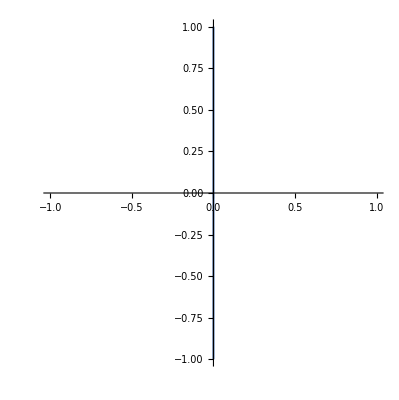

```mathematica
ParametricPlot[
{0,-Sin[ϕ]/(√2 √(1-Cos[ϕ]))}
,{ϕ,0,2π}]
```

```mathematica
{(Sin[b] Sin[a-θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Cos[a-θ] Cos[ϕ] Sin[b]-Cos[b] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ]))}/.{a->1,b->1}
```

{(Sin[1] Sin[1-θ] Sin[ϕ])/(√2 √(1-Cos[1] Cos[ϕ]-Cos[1-θ] Sin[1] Sin[ϕ])),(Cos[1-θ] Cos[ϕ] Sin[1]-Cos[1] Sin[ϕ])/(√2 √(1-Cos[1] Cos[ϕ]-Cos[1-θ] Sin[1] Sin[ϕ]))}

```mathematica
{(Sin[b] Sin[a-θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Cos[a-θ] Cos[ϕ] Sin[b]-Cos[b] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ]))}/.{a->π/2,b->π/2}
```

{(Cos[θ] Sin[ϕ])/(√2 √(1-Sin[θ] Sin[ϕ])),(Cos[ϕ] Sin[θ])/(√2 √(1-Sin[θ] Sin[ϕ]))}

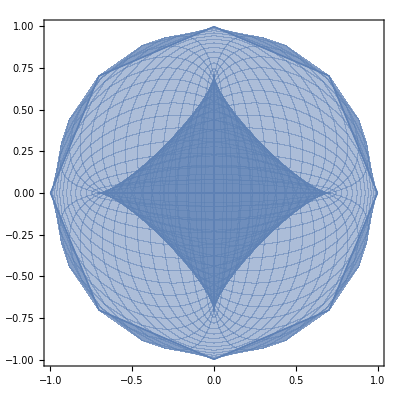

```mathematica
ParametricPlot[
{(Cos[θ] Sin[ϕ])/(√2 √(1-Sin[θ] Sin[ϕ])),(Cos[ϕ] Sin[θ])/(√2 √(1-Sin[θ] Sin[ϕ]))}
,{θ,0,2π},{ϕ,0,2π}]
```

```mathematica
ParametricPlot3D[
{(Cos[θ] Sin[ϕ])/(√2 √(1-Sin[θ] Sin[ϕ])),(Cos[ϕ] Sin[θ])/(√2 √(1-Sin[θ] Sin[ϕ])),0}
,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
{(Sin[b] Sin[a-θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Cos[a-θ] Cos[ϕ] Sin[b]-Cos[b] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ]))}/.{a->π/2,b->0}
```

{0,-Sin[ϕ]/(√2 √(1-Cos[ϕ]))}

```mathematica
ParametricPlot[
{0,-Sin[ϕ]/(√2 √(1-Cos[ϕ]))}
,{ϕ,0,2π}]
```

```mathematica
{(Sin[b] Sin[a-θ] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ])),(Cos[a-θ] Cos[ϕ] Sin[b]-Cos[b] Sin[ϕ])/(√2 √(1-Cos[b] Cos[ϕ]-Cos[a-θ] Sin[b] Sin[ϕ]))}/.{a->0,b->π/2}
```

{-(Sin[θ] Sin[ϕ])/(√2 √(1-Cos[θ] Sin[ϕ])),(Cos[θ] Cos[ϕ])/(√2 √(1-Cos[θ] Sin[ϕ]))}

```mathematica
ParametricPlot[
{0,-Sin[ϕ]/(√2 √(1-Cos[ϕ]))}
,{ϕ,0,2π}]
```

```mathematica
ParametricPlot3D[
{-(Sin[θ] Sin[ϕ])/(√2 √(1-Cos[θ] Sin[ϕ])),(Cos[θ] Cos[ϕ])/(√2 √(1-Cos[θ] Sin[ϕ])),θ}
,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{-(Sin[θ] Sin[ϕ])/(√2 √(1-Cos[θ] Sin[ϕ])),(Cos[θ] Cos[ϕ])/(√2 √(1-Cos[θ] Sin[ϕ])),ϕ}
,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
FullSimplify[
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}).{Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]},Normalize@{Cos[θ] Sin[ϕ],Cos[ϕ] Sin[θ]},Normalize@{0,-Sin[ϕ]}}
,{a,b,θ,ϕ}∈Reals]
```

$Aborted

```mathematica
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}).{Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]},Normalize@{Cos[θ] Sin[ϕ],Cos[ϕ] Sin[θ]},Normalize@{0,-Sin[ϕ]}}
```

{-((Sin[θ] Sin[ϕ] (Cos[a] Sin[b]-Cos[θ] Sin[ϕ]))/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2) √(Abs[Cos[b]-Cos[ϕ]]^2+Abs[Cos[a] Sin[b]-Cos[θ] Sin[ϕ]]^2+Abs[Sin[a] Sin[b]-Sin[θ] Sin[ϕ]]^2)))+(Cos[θ] Sin[ϕ] (Sin[a] Sin[b]-Sin[θ] Sin[ϕ]))/(√(Abs[Cos[ϕ] Sin[θ]]^2+Abs[Cos[θ] Sin[ϕ]]^2) √(Abs[Cos[b]-Cos[ϕ]]^2+Abs[Cos[a] Sin[b]-Cos[θ] Sin[ϕ]]^2+Abs[Sin[a] Sin[b]-Sin[θ] Sin[ϕ]]^2)),-((Cos[b]-Cos[ϕ]) Sin[ϕ])/(Abs[Sin[ϕ]] √(Abs[Cos[b]-Cos[ϕ]]^2+Abs[Cos[a] Sin[b]-Cos[θ] Sin[ϕ]]^2+Abs[Sin[a] Sin[b]-Sin[θ] Sin[ϕ]]^2))+(Cos[θ] Cos[ϕ] (Cos[a] Sin[b]-Cos[θ] Sin[ϕ]))/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2) √(Abs[Cos[b]-Cos[ϕ]]^2+Abs[Cos[a] Sin[b]-Cos[θ] Sin[ϕ]]^2+Abs[Sin[a] Sin[b]-Sin[θ] Sin[ϕ]]^2))+(Cos[ϕ] Sin[θ] (Sin[a] Sin[b]-Sin[θ] Sin[ϕ]))/(√(Abs[Cos[ϕ] Sin[θ]]^2+Abs[Cos[θ] Sin[ϕ]]^2) √(Abs[Cos[b]-Cos[ϕ]]^2+Abs[Cos[a] Sin[b]-Cos[θ] Sin[ϕ]]^2+Abs[Sin[a] Sin[b]-Sin[θ] Sin[ϕ]]^2))}

```mathematica
FullSimplify[
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[c] Sin[d],Sin[c] Sin[d],Cos[d]}).{Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]},Normalize@{Cos[θ] Sin[ϕ],Cos[ϕ] Sin[θ]},Normalize@{0,-Sin[ϕ]}}
,{a,b,θ,ϕ}∈Reals]
```

$Aborted

```mathematica
FullSimplify[
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[c] Sin[d],Sin[c] Sin[d],Cos[d]}).{Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]},Normalize@{Cos[θ] Sin[ϕ],Cos[ϕ] Sin[θ]},Normalize@{0,-Sin[ϕ]}}
,{a,b,c,d,θ,ϕ}∈Reals]
```

$Aborted

```mathematica
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[c] Sin[d],Sin[c] Sin[d],Cos[d]}).{Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]},Normalize@{Cos[θ] Sin[ϕ],Cos[ϕ] Sin[θ]},Normalize@{0,-Sin[ϕ]}}
```

{(Cos[θ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[ϕ])/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) √(Abs[Cos[ϕ] Sin[θ]]^2+Abs[Cos[θ] Sin[ϕ]]^2))-((Cos[a] Sin[b]-Cos[c] Sin[d]) Sin[θ] Sin[ϕ])/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) √(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2)),(Cos[θ] Cos[ϕ] (Cos[a] Sin[b]-Cos[c] Sin[d]))/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) √(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2))+(Cos[ϕ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[θ])/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) √(Abs[Cos[ϕ] Sin[θ]]^2+Abs[Cos[θ] Sin[ϕ]]^2))-((Cos[b]-Cos[d]) Sin[ϕ])/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) Abs[Sin[ϕ]])}

```mathematica
Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]}
```

{-(Sin[θ] Sin[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2)),(Cos[θ] Cos[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2))}

```mathematica
FullSimplify[
Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]}
,{θ,ϕ,Sin[θ]}∈Reals]
```

{-(Sin[θ] Sin[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2)),(Cos[θ] Cos[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2))}

```mathematica
FullSimplify[
Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]}
,{θ,ϕ,Sin[θ],Sin[ϕ],Cos[θ],Cos[ϕ]}∈Reals]
```

{-(Sin[θ] Sin[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2)),(Cos[θ] Cos[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2))}

```mathematica
FullSimplify[
Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]}
,{θ,ϕ,Sin[θ]Sin[ϕ],Cos[θ] Cos[ϕ]}∈Reals]
```

{-(Sin[θ] Sin[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2)),(Cos[θ] Cos[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2))}

```mathematica
Normalize@{-Sin[θ] Sin[ϕ],Cos[θ] Cos[ϕ]}
```

{-(Sin[θ] Sin[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2)),(Cos[θ] Cos[ϕ])/(√(Abs[Cos[θ] Cos[ϕ]]^2+Abs[Sin[θ] Sin[ϕ]]^2))}

```mathematica
Normalize@{Cos[θ] Sin[ϕ],Cos[ϕ] Sin[θ]}
```

{(Cos[θ] Sin[ϕ])/(√(Abs[Cos[ϕ] Sin[θ]]^2+Abs[Cos[θ] Sin[ϕ]]^2)),(Cos[ϕ] Sin[θ])/(√(Abs[Cos[ϕ] Sin[θ]]^2+Abs[Cos[θ] Sin[ϕ]]^2))}

```mathematica
Normalize@{0,-Sin[ϕ]}
```

{0,-Sin[ϕ]/Abs[Sin[ϕ]]}

```mathematica
{-(Sin[θ] Sin[ϕ])/(√((Cos[θ] Cos[ϕ])^2+(Sin[θ] Sin[ϕ])^2)),(Cos[θ] Cos[ϕ])/(√((Cos[θ] Cos[ϕ])^2+(Sin[θ] Sin[ϕ])^2))}
```

{-(Sin[θ] Sin[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),(Cos[θ] Cos[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))}

```mathematica
{(Cos[θ] Sin[ϕ])/(√((Cos[ϕ] Sin[θ])^2+(Cos[θ] Sin[ϕ])^2)),(Cos[ϕ] Sin[θ])/(√((Cos[ϕ] Sin[θ])^2+(Cos[θ] Sin[ϕ])^2))}
```

{(Cos[θ] Sin[ϕ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2)),(Cos[ϕ] Sin[θ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))}

```mathematica
{0,-Sin[ϕ]/Abs[Sin[ϕ]]}
```

{0,-Sin[ϕ]/Abs[Sin[ϕ]]}

```mathematica
{
{-(Sin[θ] Sin[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),(Cos[θ] Cos[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))},
{(Cos[θ] Sin[ϕ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2)),(Cos[ϕ] Sin[θ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))},
{0,-Sin[ϕ]/Abs[Sin[ϕ]]}
}
```

{{-(Sin[θ] Sin[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),(Cos[θ] Cos[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))},{(Cos[θ] Sin[ϕ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2)),(Cos[ϕ] Sin[θ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))},{0,-Sin[ϕ]/Abs[Sin[ϕ]]}}

```mathematica
FullSimplify[
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[c] Sin[d],Sin[c] Sin[d],Cos[d]}).{{-(Sin[θ] Sin[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),(Cos[θ] Cos[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))},{(Cos[θ] Sin[ϕ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2)),(Cos[ϕ] Sin[θ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))},{0,-Sin[ϕ]/Abs[Sin[ϕ]]}}
,{a,b,c,d,θ,ϕ}∈Reals]
```

$Aborted

```mathematica
Normalize@({Cos[a] Sin[b],Sin[a] Sin[b],Cos[b]}-{Cos[c] Sin[d],Sin[c] Sin[d],Cos[d]}).{{-(Sin[θ] Sin[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),(Cos[θ] Cos[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))},{(Cos[θ] Sin[ϕ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2)),(Cos[ϕ] Sin[θ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))},{0,-Sin[ϕ]/Abs[Sin[ϕ]]}}
```

{(Cos[θ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[ϕ])/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))-((Cos[a] Sin[b]-Cos[c] Sin[d]) Sin[θ] Sin[ϕ])/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),-((Cos[b]-Cos[d]) Sin[ϕ])/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) Abs[Sin[ϕ]])+(Cos[ϕ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[θ])/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))+(Cos[θ] Cos[ϕ] (Cos[a] Sin[b]-Cos[c] Sin[d]))/(√(Abs[Cos[b]-Cos[d]]^2+Abs[Cos[a] Sin[b]-Cos[c] Sin[d]]^2+Abs[Sin[a] Sin[b]-Sin[c] Sin[d]]^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))}

```mathematica
{(Cos[θ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[ϕ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))-((Cos[a] Sin[b]-Cos[c] Sin[d]) Sin[θ] Sin[ϕ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),-((Cos[b]-Cos[d]) Sin[ϕ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) Abs[Sin[ϕ]])+(Cos[ϕ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[θ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))+(Cos[θ] Cos[ϕ] (Cos[a] Sin[b]-Cos[c] Sin[d]))/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))}
```

{(Cos[θ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[ϕ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))-((Cos[a] Sin[b]-Cos[c] Sin[d]) Sin[θ] Sin[ϕ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),-((Cos[b]-Cos[d]) Sin[ϕ])/(Abs[Sin[ϕ]] √((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2))+(Cos[ϕ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[θ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))+(Cos[θ] Cos[ϕ] (Cos[a] Sin[b]-Cos[c] Sin[d]))/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))}

```mathematica
{(Cos[θ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[ϕ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))-((Cos[a] Sin[b]-Cos[c] Sin[d]) Sin[θ] Sin[ϕ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),-((Cos[b]-Cos[d]) Sin[ϕ])/(Abs[Sin[ϕ]] √((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2))+(Cos[ϕ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[θ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))+(Cos[θ] Cos[ϕ] (Cos[a] Sin[b]-Cos[c] Sin[d]))/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))}/.{a->0,b->0,c->0,d->0}
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression (0 Cos[θ] ComplexInfinity Sin[ϕ])/(√(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2)) encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression (0 ComplexInfinity Sin[θ] Sin[ϕ])/(√(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)) encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0 ComplexInfinity Sin[ϕ])/Abs[Sin[ϕ]] encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate}

```mathematica
{(Cos[θ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[ϕ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))-((Cos[a] Sin[b]-Cos[c] Sin[d]) Sin[θ] Sin[ϕ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)),-((Cos[b]-Cos[d]) Sin[ϕ])/(Abs[Sin[ϕ]] √((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2))+(Cos[ϕ] (Sin[a] Sin[b]-Sin[c] Sin[d]) Sin[θ])/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))+(Cos[θ] Cos[ϕ] (Cos[a] Sin[b]-Cos[c] Sin[d]))/(√((Cos[b]-Cos[d])^2+(Cos[a] Sin[b]-Cos[c] Sin[d])^2+(Sin[a] Sin[b]-Sin[c] Sin[d])^2) √(Cos[θ]^2 Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2))}/.{a->0,b->0,c->π/2,d->π/2}
```

{-(Cos[θ] Sin[ϕ])/(√2 √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2)),-Sin[ϕ]/(√2 Abs[Sin[ϕ]])-(Cos[ϕ] Sin[θ])/(√2 √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

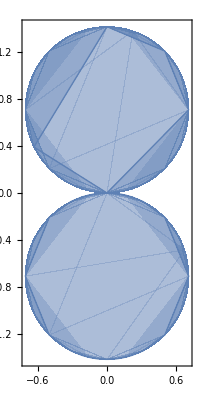

```mathematica
ParametricPlot[
{-(Cos[θ] Sin[ϕ])/(√2 √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2)),-Sin[ϕ]/(√2 Abs[Sin[ϕ]])-(Cos[ϕ] Sin[θ])/(√2 √(Cos[ϕ]^2 Sin[θ]^2+Cos[θ]^2 Sin[ϕ]^2))}
,{θ,0,2π},{ϕ,0,2π}]
```

```mathematica
Div[f[x,y],{x,y}]
```

Div::sclr: The scalar expression f[x,y] does not have a divergence.

f[x,y]{x,y}

```mathematica
∇_x .f[x]
```

f[x]x

```mathematica
∇_{x,y} .f[x,y]
```

Div::sclr: The scalar expression f[x,y] does not have a divergence.

f[x,y]{x,y}



```mathematica
ParametricPlot[
{Cos[t],Sin[t]}
,{t,0,2π}]
```

```mathematica
D[{Cos[t],Sin[t]},t]
```

{-Sin[t],Cos[t]}

```mathematica
∇_t f[t]
```

f[t]t

```mathematica
∇_t {x[t],y[t]}
```

{x[t],y[t]}t

```mathematica
∇_t {Cos[t],Sin[t]}
```

{Cos[t],Sin[t]}t

```mathematica
Grad[{Cos[t],Sin[t]},{t}]
```

{{-Sin[t]},{Cos[t]}}

```mathematica
Normalize@{-Sin[t],Cos[t]}
```

{-Sin[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2)),Cos[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2))}

```mathematica
FullSimplify[Normalize@{-Sin[t],Cos[t]},t∈Reals]
```

{-Sin[t],Cos[t]}

```mathematica
FullSimplify[Normalize[{Cos[a],Sin[a]}-{Cos[b],Sin[b]}].{-Sin[t],Cos[t]},{a,b,t}∈Reals∧0≤a≤2π∧0≤b≤2π∧a>b∧0≤t≤2π]
```

(Sin[a-t]-Sin[b-t])/(2 Abs[Sin[(a-b)/2]])

```mathematica
Manipulate[Plot[(Sin[a-t]-Sin[b-t])/(2 Abs[Sin[(a-b)/2]]),{t,-5.283185307179586,7.283185307179586}],{a,-5.283185307179586,7.283185307179586},{b,-2,2}]
```

```mathematica
(Sin[a-t]-Sin[b-t])/(2 Abs[Sin[(a-b)/2]])
```

```mathematica
FullSimplify[Normalize[{Cos[a],Sin[a]}-{Cos[b],Sin[b]}].{-Sin[t],Cos[t]},{a,b,t}∈Reals∧0≤a≤2π∧0≤b≤2π∧0≤t≤2π]
```

(Sin[a-t]-Sin[b-t])/(2 Abs[Sin[(a-b)/2]])

```mathematica
(Sin[a-t]-Sin[b-t])/(2 Abs[Sin[(a-b)/2]])/.{a->0,b->π/2}
```

(-Cos[t]-Sin[t])/(√2)

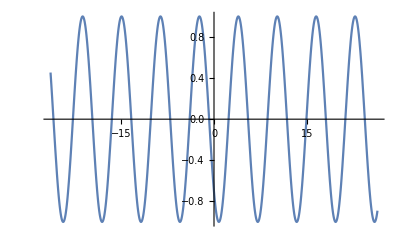

```mathematica
Plot[(-Cos[t]-Sin[t])/(√2),{t,-26.389378290154262,26.389378290154262}]
```

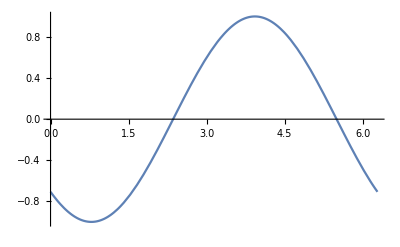

```mathematica
Plot[(-Cos[t]-Sin[t])/(√2),{t,0,2π}]
```

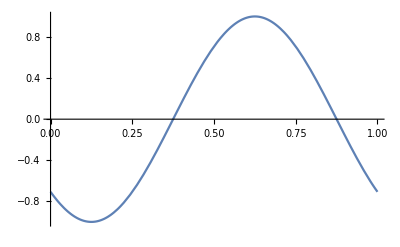

```mathematica
Plot[(-Cos[2π t]-Sin[2π t])/(√2),{t,0,1}]
```

```mathematica
Reduce[(-Cos[2π t]-Sin[2π t])/(√2)==1,t,Reals]
```

C[1]∈ℤ&&t==(-2 ArcTan[1/(-1+√2)]+2 π C[1])/(2 π)

```mathematica
Integrate[(-Cos[2π t]-Sin[2π t])/(√2),{t,0,1}]
```

0

```mathematica
FullSimplify[
Normalize[{Cos[a],Sin[a]}-{Cos[b],Sin[b]}].{-Sin[t],Cos[t]}
,{a,b,t}∈Reals∧0≤a≤2π∧0≤b≤2π∧a>b∧0≤t≤2π]
```

(Sin[a-t]-Sin[b-t])/(2 Abs[Sin[(a-b)/2]])

```mathematica
(Sin[a-t]-Sin[b-t])/(2 Abs[Sin[(a-b)/2]])/.{a->π/2,b->0}
```

(Cos[t]+Sin[t])/(√2)

```mathematica
(Cos[t]+Sin[t])/(√2)
```

(Cos[t]+Sin[t])/(√2)

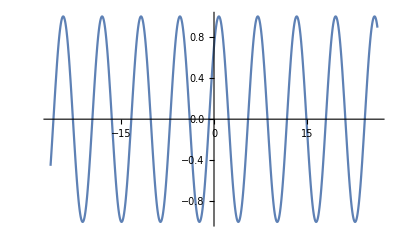

```mathematica
Plot[(Cos[t]+Sin[t])/(√2),{t,-26.389378290154262,26.389378290154262}]
```

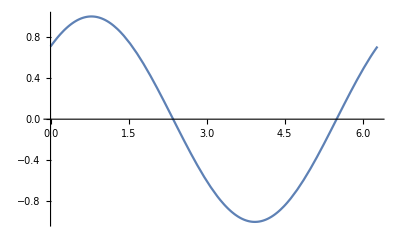

```mathematica
Plot[(Cos[t]+Sin[t])/(√2),{t,0,2 π}]
```

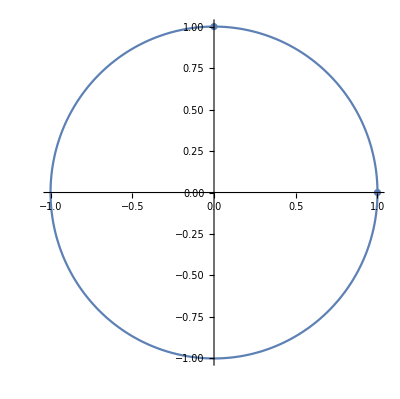

```mathematica
Show[{
ParametricPlot[
{Cos[t],Sin[t]}
,{t,0,2π}],
ListPlot[{{1,0},{0,1}}]
}]
```